## Minimum-Time Planar Paths with L2 Velocity and Acceleration Constraints and a Limited Number of Constant Acceleration Inputs interactive demonstrations of the solution and generates Figs. 6, 7, and 8. Authors: Aaron Becker (atbecker@uh.edu) and Victor Montano Baez (VMontano.Baez@gmail.com) Last updated Friday March 17, 2023

## Interactive Demonstration

```mathematica
Manipulate[Module[{v0,vG,p0,pV,pG,pGv,v0x,v0y,p0x,p0y,pGx,pGy,vGx,vGy,
solt1,solθ1,maxV1, tMax1,solt2,solθ2,maxV2, tMax2,θf,tf,ϕf,τf,pt,mt,at,vt,solt1b,solθ1b,solt2b,solθ2b,p,
ansFR,t,τ,θ,ϕ,midPt,pts,t2, maxV,pθt1,vθt1
},
{p0,pV,pG,pGv} = loc;
p = Min[pin,1];
v0 =pV-p0; (*compute the initial velocity*)
vG =pGv-pG; (*compute the initial velocity*)
(*If[ locOld!= loc ,*)
If[ Norm[v0]>mV, v0= Normalize[v0]*mV; loc⟦2⟧ =p0+v0; ]; (*Limit the initial velocity*)
If[ Norm[vG]>mV, vG= Normalize[vG]*mV; loc⟦4⟧ =pG+vG; ]; (*Limit the final velocity*)
(*locOld=loc; 
];*)
{v0x,v0y}=v0;
{p0x,p0y}=p0;
{pGx,pGy}=pG;
{vGx,vGy}=vG;
midPt = (p0+Normalize[v0]*1/2*Norm[v0]^2 /mA +pG -Normalize[vG]*1/2*Norm[vG]^2 /mA)/2; 
pts = {p0,p0+1/2*Normalize[v0]*Norm[v0]^2 /mA ,midPt, pG -1/2*Normalize[vG]*Norm[vG]^2 /mA,pG};
{solt1,solθ1,{maxV1, tMax1}}=findAccelSolAna[p0,pts⟦5⟧,v0,mA];
{solt2,solθ2,{maxV2, tMax2}}=findAccelSolAna[pG,pts⟦1⟧,-vG,mA];

Quiet[ansFR=FindRoot[  
{   p0x+v0x*Abs[t]+mA/2 Cos[θ] t^2==pGx-vGx*Abs[τ]+mA/2Cos[ϕ] τ^2&&
p0y+v0y*Abs[t]+mA/2Sin[θ] t^2==pGy-vGy*Abs[τ]+mA/2Sin[ϕ] τ^2&&
v0x+mA Cos[θ]Abs[t]==vGx -  mA Cos[ϕ]Abs[τ]&&
v0y+mA Sin[θ]Abs[t]==vGy -  mA Sin[ϕ]Abs[τ]}, 
{{t,solt1},{τ,solt2},{θ,solθ1},{ϕ,solθ2}}]];
{t,τ,θ,ϕ}={Abs[t],Abs[τ],θ,ϕ}/.ansFR;

If[ Norm[computeErr[p0,pG,v0,vG,t,τ,θ,ϕ,mA]]>0.0001,
{solt1b,solθ1b,{maxV1, tMax1}}=findAccelSolAna[p0,pts⟦4⟧,v0,mA];
{solt2b,solθ2b,{maxV2, tMax2}}=findAccelSolAna[pG,pts⟦2⟧,-vG,mA];
Quiet[ansFR=FindRoot[
{   p0x+v0x*Abs[t]+mA/2 Cos[θ] t^2==pGx-vGx*Abs[τ]+mA/2Cos[ϕ] τ^2&&
p0y+v0y*Abs[t]+mA/2Sin[θ] t^2==pGy-vGy*Abs[τ]+mA/2Sin[ϕ] τ^2&&
v0x+mA Cos[θ]Abs[t]==vGx -  mA Cos[ϕ]Abs[τ]&&
v0y+mA Sin[θ]Abs[t]==vGy -  mA Sin[ϕ]Abs[τ]}, 
{{t,solt1b},{τ,solt2b},{θ,solθ1b},{ϕ,solθ2b}}];
{t,τ,θ,ϕ}={Abs[t],Abs[τ],θ,ϕ}/.ansFR;]];

If[ Norm[computeErr[p0,pG,v0,vG,t,τ,θ,ϕ,mA]]>0.0001,
(*Print[StringForm["second try failed, trying again, Error is {x,y,vx,vy} = ``",Chop[computeErr[p0,pG,v0,vG,t,τ,θ,ϕ,mA]]]];*)
Quiet[ansFR=FindRoot[
{   p0x+v0x*Abs[t]+mA/2 Cos[θ] t^2==pGx-vGx*Abs[τ]+mA/2Cos[ϕ] τ^2&&
p0y+v0y*Abs[t]+mA/2Sin[θ] t^2==pGy-vGy*Abs[τ]+mA/2Sin[ϕ] τ^2&&
v0x+mA Cos[θ]Abs[t]==vGx -  mA Cos[ϕ]Abs[τ]&&
v0y+mA Sin[θ]Abs[t]==vGy -  mA Sin[ϕ]Abs[τ]}, 
{{t,solt1,solt1b},{τ,solt2,solt2b},{θ,solθ1,solθ1b},{ϕ,solθ2,solθ2b}}];
{t,τ,θ,ϕ}={Abs[t],Abs[τ],θ,ϕ}/.ansFR;]];

If[ Norm[computeErr[p0,pG,v0,vG,t,τ,θ,ϕ,mA]]>0.0001,
(*Print[StringForm["third try failed, trying again, Error is {x,y,vx,vy} = ``",Chop[computeErr[p0,pG,v0,vG,t,τ,θ,ϕ,mA]]]];*)
{solt1,solθ1,{maxV1, tMax1}}=findAccelSolAna[p0,pts⟦3⟧,v0,mA];
{solt2,solθ2,{maxV2, tMax2}}=findAccelSolAna[pG,pts⟦3⟧,-vG,mA];
Quiet[ansFR=FindRoot[
{   p0x+v0x*Abs[t]+mA/2 Cos[θ] t^2==pGx-vGx*Abs[τ]+mA/2Cos[ϕ] τ^2&&
p0y+v0y*Abs[t]+mA/2Sin[θ] t^2==pGy-vGy*Abs[τ]+mA/2Sin[ϕ] τ^2&&
v0x+mA Cos[θ]Abs[t]==vGx -  mA Cos[ϕ]Abs[τ]&&
v0y+mA Sin[θ]Abs[t]==vGy -  mA Sin[ϕ]Abs[τ]}, 
{{t,solt1},{τ,solt2},{θ,solθ1},{ϕ,solθ2}}];
{t,τ,θ,ϕ}={Abs[t],Abs[τ],θ,ϕ}/.ansFR;]];
t2 = 0;


 maxV = Norm[twoBangBangV[p0,v0,t,τ,θ,ϕ,t,mA]];
If[  maxV >mV,
Module[{err,i,minVal=0.0001},
err = 50;i = 1;
While[err>minVal && i<Length[stPts],
{θ,ϕ}=Quiet[numSolveStartAndEndVelCoastTANequation[p0,pG,v0,vG,mA,mV,stPts⟦i⟧ ]];
err=computeError3Step[p0,v0,pG,vG,θ,ϕ,mA,mV];
i=i+1;];
];

{t,t2,τ}=calctmVV[p0,pG,v0,vG,mA,mV,θ,ϕ];
];

mt = p*(t+τ+t2);

pt=posVV[mt,p0,v0,mA,mV,θ,ϕ,{t,t2,τ}];
vt=velVV[mt,p0,v0,mA,mV,θ,ϕ,{t,t2,τ}];
at=accVV[mt,p0,v0,mA,mV,θ,ϕ,{t,t2,τ}];

ParametricPlot[
{If[velocityboundT1,posT1[tim 2 π,p0,v0,mA,mV],p0],
If[velocityboundT3,posT1[tim 2 π,pG,-vG,mA,mV],pG],
posVV[tim(t+t2+τ),p0,v0,mA,mV,θ,ϕ,{t,t2,τ}]},

{tim,0,1},Axes->showAxis,
PlotStyle->{ColorData[97,"ColorList"]⟦1⟧,ColorData[97,"ColorList"]⟦2⟧,Red},

Epilog->{PointSize[Medium],Blue,Arrow[{p0,p0+v0}], Point[p0],Black, 
Point[posVV[(t         ),p0,v0,mA,mV,θ,ϕ,{t,t2,τ}]],
Point[posVV[(t+t2),p0,v0,mA,mV,θ,ϕ,{t,t2,τ}]],
Darker[Green],Point[pG],Arrow[{pG,pG+vG}],
(*{Purple,Thin,
Point[pts],Line[pts]},*)
Purple,Point[pt]
,Arrowheads[0.03],Arrow[{pt,pt+vt}],Darker[Orange],Arrow[{pt,pt+at}]

}
,Prolog->{If[rocket,{(*Rocket*)
drawRocketThrust[pt,at]}],
Arrowheads[0.03],Thin,
If[arrowsT1,Table[pθt1=Flatten[posT1[θv,p0,v0,mA,mV]] ;vθt1=Flatten[velT1[θv,p0,v0,mA,mV]];{LightGray,HalfLine[{pθt1,pθt1+vθt1}],Pink,  Arrow[{pθt1,pθt1+vθt1}]},{θv,-π,π,π/16}],Point[{100,100}]],
If[arrowsT3,Table[pθt1=Flatten[posT1[θv,pG,-vG,mA,mV]] ;vθt1=Flatten[velT1[θv,pG,-vG,mA,mV]];{Lighter[Orange],{Dashed,HalfLine[{pθt1,pθt1+vθt1}]},Darker[Orange],  Arrow[{pθt1+vθt1,pθt1}]},{θv,-π,π,π/16}],Point[{100,100}]]
} ,
ImageSize->Medium,

AxesOrigin->{0,0},PlotRange->{{-5,5},{-5,5}}]],
{{mA,0.5},0.1,2,0.01,Appearance->"Labeled"},{{mV,1.25},0.01,6,0.01,Appearance->"Labeled"},
{{loc,{{-3,2},{-2.5,2.5},{3,-2},{2.5,-2.5}}},{-5,-5},{5,5},Locator,Appearance->None},{{locOld,{{-1,-1},{-1,-1},{-1,-1},{-1,-1}}},ControlType->None},
{{pin,0.},0,1.1(*,Appearance->"Labeled"*)},
{{rocket,True},{False,True}},
{{velocityboundT1,True},{False,True}},
{{velocityboundT3,True},{False,True}},
{{arrowsT1,True},{False,True}},
{{arrowsT3,True},{False,True}},
{{showAxis,True},{False,True}},
{{stPts ,N[2*π vanDerCorput[500,2]-π]},ControlType->None},
SaveDefinitions->True
]
```

## Completion times vs initial direction plot (Fig. 6)

```mathematica
Example from [1, 1] to stop at [-1, -1] with full velocity in angle D at start, with Subscript[v, m]=Subscript[a, m]
```

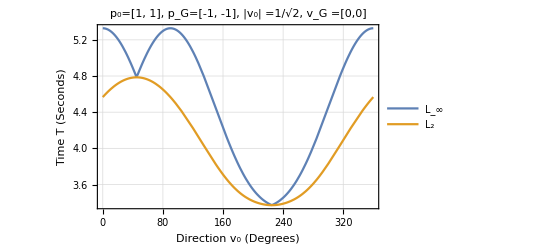

```mathematica
Module[{iterations,p0,pG,vG,andD,mV,mA,pL2diag},
iterations = 12;
p0  ={1,1};
pG = {-1,-1};
vG = {0,0};(*vG = {-0.5,-0};*)
(*angD = -135;*)
mV = 1;
mA = 1;
(*Change PerformanceGoal->"Speed" to PerformanceGoal->"Quality" for the final version!*)
pL2diag =Plot[{calculateTimeToGoalLInf[p0,pG,mV/(√2){Cos[angD °],Sin[angD °]},vG,mA 1/(√2),mV 1/(√2)],calculateTimeToGoalL2[p0,pG,mV/(√2){Cos[angD °],Sin[angD °]},vG,mA,mV,iterations]},{angD,0,360},PlotLegends->Placed[{"L_∞","L_2"},{0.62,0.7}],PlotLabel->"p_0=[1, 1], p_G=[-1, -1], |v_0| =1/√2, v_G =[0,0]",PerformanceGoal->"Speed",Epilog->Inset[boundsGraphics,{50,3.8},{0,0},100]

];
Show[pL2diag, timesPlotSettings]]
```

## Total path lengths vs initial direction plot (Fig. 7)

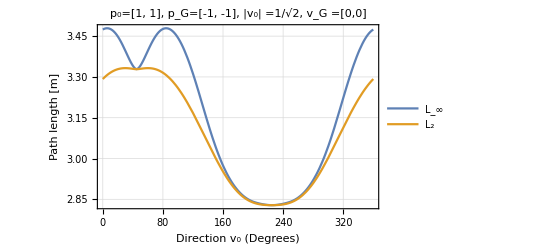

```mathematica
Module[{iterations,p0,pG,vG,mV,mA,pL2diag,displacementsPlots,v0Mag,displacementsL2AndLinfPlot,pGv, ang, v0Dir,dispL2},
p0  ={1,1};
v0Mag = N[Norm[{1/2,1/2}]];
(*v0Mag = mV/N[Sqrt[2]];*)(*from previous example*)
v0Dir = {Cos[ang], Sin[ang]};
pG = {-1,-1};
vG = {0,0};(*vG = {-0.5,-0};*)
mA=1;
mV = 1;
(*pGv = {0,-1};*) (* should evaluate to pG for stop at goal *) 
pGv = vG + pG; 

displacementsL2AndLinfPlot =Plot[{
calculateDispLInf2[p0,pG,v0Mag*{Cos[angD °],Sin[angD °]},vG,mA,mV],
calcDispL2[p0,pG,v0Mag*{Cos[angD °],Sin[angD °]},vG,mA,mV]} ,{angD,0,360},PlotLegends->Placed[{"L_∞","L_2"},{0.62,0.7}], PlotLabel->"p_0=[1, 1], p_G=[-1, -1], |v_0| =1/√2, v_G =[0,0]",PerformanceGoal->"Speed",Frame->{True},GridLines->Automatic,FrameLabel->{"Direction v_0 (Degrees)","Path length [m]"}];
Show[displacementsL2AndLinfPlot]

]
```

## L2 and L∞ trajectories; position, velocity, and acceleration profiles (Fig. 8)

```mathematica
Trajectory for L2 that never coasts and stops at goal
```

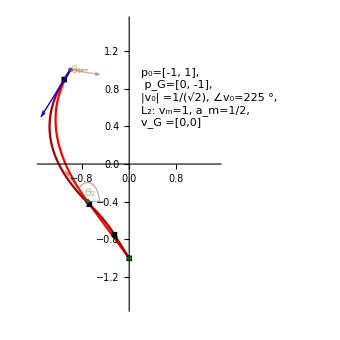
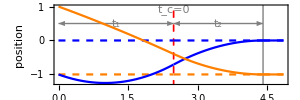
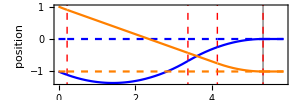
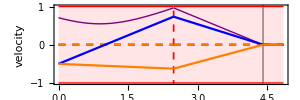
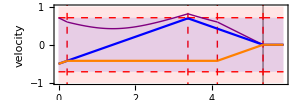
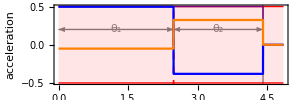
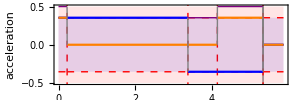
-Graphics- | L_2 Profiles | L_∞ Profiles
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Module[{tMax,pPlot,vPlot,aPlot,stPts,tMaxL2,pPlotL2,vPlotL2,aPlotL2,p0,pV,pG,pGv,mA,mV,tMaxLInf,pPlotLInf,vPlotLInf,aPlotLInf,profilePlots,trajPlotL2,plotRange,trajPlotLInf,trajPlotGraphics,figs,v0,vG,v0Dir,angD,v0Mag,ang,figsCol,LInfSwitchPoints},
p0  ={-1,1};
v0Mag = Norm[{1/2,1/2}];
(*v0Mag = mV/N[Sqrt[2]];*)(*from previous example*)
ang = 225 Degree;
v0Dir = {Cos[ang], Sin[ang]};
pG = {0,-1};
vG = {0,0};(*vG = {-0.5,-0};*)
angD = -135;
mA=1/2;
mV = 1;
(*pGv = {0,-1};*) (* should evaluate to pG for stop at goal *) 
pGv = vG + pG; 
(*pV= {-1.5,.5};*)
pV = N[v0Mag]*v0Dir + p0;
(*No coast, stops at goal*)
plotRange = {{-1.5,1.5},{-1.5,1.5}} ;


{trajPlotL2,tMaxL2,pPlotL2,vPlotL2,aPlotL2}=getL2TrajAndProfiles[p0,pV,pG,pGv,mA,mV,plotRange];
{trajPlotLInf,tMaxLInf,pPlotLInf,vPlotLInf,aPlotLInf,LInfSwitchPoints}=getLInfTrajAndProfiles[p0,pV,pG,pGv,mA,mV];
profilePlots = Multicolumn[{Style["L_2 Profiles" ,FontFamily->"Arial"],pPlotL2,vPlotL2,aPlotL2,Style["L_∞ Profiles" ,FontFamily->"Arial"],pPlotLInf,vPlotLInf,aPlotLInf},{4,2},Alignment->Center];
figs = Show[trajPlotL2,trajPlotLInf,LInfSwitchPoints,Graphics[Text[StringForm["p_0=[``, ``],
 p_G=[``, ``], 
|v_0| =``, ∠v_0=``, 
L_2: v_m=``, a_m=``, 
v_G =[``,``]",p0⟦1⟧,p0⟦2⟧,pG⟦1⟧,pG⟦2⟧,v0Mag, ang,mV,mA, vG⟦1⟧,vG⟦2⟧],{0.2,0.7},{Left,Center}]],ImageSize ->340];
Multicolumn[{figs,profilePlots},{1,2}]
]
```

```mathematica
Trajectory for L2 that coasts and stops at goal
```

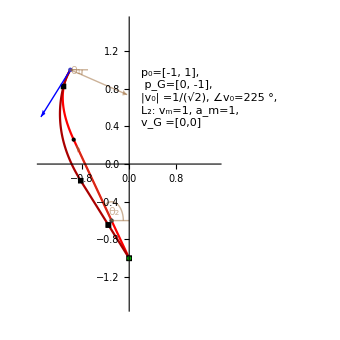
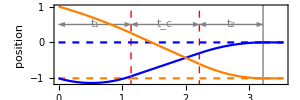
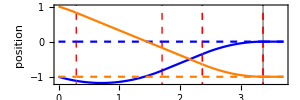
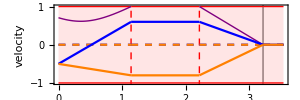
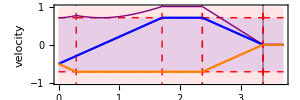
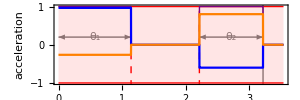
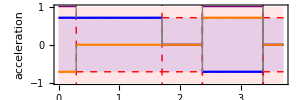
-Graphics- | L_2 Profiles | L_∞ Profiles
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Module[{tMax,pPlot,vPlot,aPlot,stPts,tMaxL2,pPlotL2,vPlotL2,aPlotL2,p0,pV,pG,pGv,mA,mV,tMaxLInf,pPlotLInf,vPlotLInf,aPlotLInf,profilePlots,trajPlotL2,plotRange,trajPlotLInf,trajPlotGraphics,figs,v0,vG,v0Dir,angD,v0Mag,ang,figsCol,LInfSwitchPoints},
p0  ={-1,1};
v0Mag = Norm[{1/2,1/2}];
(*v0Mag = mV/N[Sqrt[2]];*)(*from previous example*)
ang = 225 Degree;
v0Dir = {Cos[ang], Sin[ang]};

pG = {0,-1};
vG = {0,0};(*vG = {-0.5,-0};*)
angD = -135;
mA=1;
mV = 1;
(*pGv = {0,-1};*) (* should evaluate to pG for stop at goal *) 
pGv = vG + pG; 
(*pV= {-1.5,.5};*)
pV = N[v0Mag]*v0Dir + p0;
(*No coast, stops at goal*)
plotRange = {{-1.5,1.5},{-1.5,1.5}} ;


{trajPlotL2,tMaxL2,pPlotL2,vPlotL2,aPlotL2}=getL2TrajAndProfiles[p0,pV,pG,pGv,mA,mV,plotRange];
{trajPlotLInf,tMaxLInf,pPlotLInf,vPlotLInf,aPlotLInf,LInfSwitchPoints}=getLInfTrajAndProfiles[p0,pV,pG,pGv,mA,mV];
profilePlots = Multicolumn[{Style["L_2 Profiles" ,FontFamily->"Arial"],pPlotL2,vPlotL2,aPlotL2,Style["L_∞ Profiles" ,FontFamily->"Arial"] ,pPlotLInf,vPlotLInf,aPlotLInf},{4,2},Alignment->Center];
figs = Show[trajPlotL2,trajPlotLInf,LInfSwitchPoints,Graphics[Text[StringForm["p_0=[``, ``],
 p_G=[``, ``], 
|v_0| =``, ∠v_0=``, 
L_2: v_m=``, a_m=``, 
v_G =[``,``]",p0⟦1⟧,p0⟦2⟧,pG⟦1⟧,pG⟦2⟧,v0Mag, ang,mV,mA, vG⟦1⟧,vG⟦2⟧],{0.2,0.7},{Left,Center}]],ImageSize ->340];
Multicolumn[{figs,profilePlots},{1,2}]
]
```

```mathematica
Trajectory for L2 that never coasts and has ending velocity
```

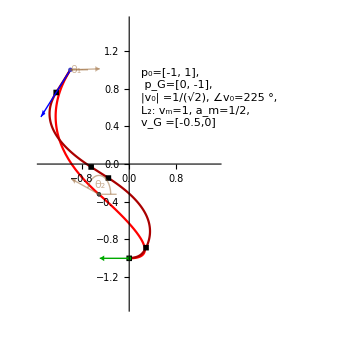
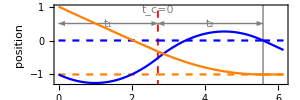
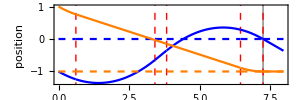
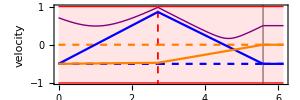
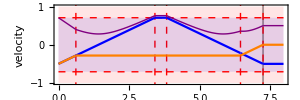
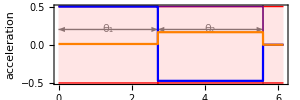
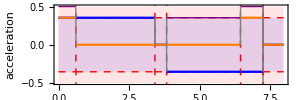
-Graphics- | L_2 Profiles | L_∞ Profiles
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Module[{tMax,pPlot,vPlot,aPlot,stPts,tMaxL2,pPlotL2,vPlotL2,aPlotL2,p0,pV,pG,pGv,mA,mV,tMaxLInf,pPlotLInf,vPlotLInf,aPlotLInf,profilePlots,trajPlotL2,plotRange,trajPlotLInf,trajPlotGraphics,figs,v0,vG,v0Dir,angD,v0Mag,ang,figsCol,LInfSwitchPoints},

p0  ={-1,1};
v0Mag = Norm[{1/2,1/2}];
(*v0Mag = mV/N[Sqrt[2]];*)(*from previous example*)
ang = 225 Degree;
v0Dir = {Cos[ang], Sin[ang]};
pG = {0,-1};
vG = {-.5,0};(*vG = {-0.5,-0};*)
angD = -135;
mA=1/2;
mV = 1;
(*pGv = {0,-1};*) (* should evaluate to pG for stop at goal *) 
pGv = vG + pG; 
(*pV= {-1.5,.5};*)
pV =N[ v0Mag]*v0Dir + p0;
(*No coast, stops at goal*)
plotRange = {{-1.5,1.5},{-1.5,1.5}} ;
{trajPlotL2,tMaxL2,pPlotL2,vPlotL2,aPlotL2}=getL2TrajAndProfiles[p0,pV,pG,pGv,mA,mV,plotRange];
{trajPlotLInf,tMaxLInf,pPlotLInf,vPlotLInf,aPlotLInf,LInfSwitchPoints}=getLInfTrajAndProfiles[p0,pV,pG,pGv,mA,mV];
profilePlots = Multicolumn[{Style["L_2 Profiles" ,FontFamily->"Arial"],pPlotL2,vPlotL2,aPlotL2,Style["L_∞ Profiles" ,FontFamily->"Arial"],pPlotLInf,vPlotLInf,aPlotLInf},{4,2},Alignment->Center];
figs = Show[trajPlotL2,trajPlotLInf,LInfSwitchPoints,Graphics[Text[StringForm["p_0=[``, ``],
 p_G=[``, ``], 
|v_0| =``, ∠v_0=``, 
L_2: v_m=``, a_m=``, 
v_G =[``,``]",p0⟦1⟧,p0⟦2⟧,pG⟦1⟧,pG⟦2⟧,v0Mag, ang,mV,mA, vG⟦1⟧,vG⟦2⟧],{0.2,0.7},{Left,Center}]],ImageSize ->340];
Multicolumn[{figs,profilePlots},{1,2}]
]
```

```mathematica
Another one
```

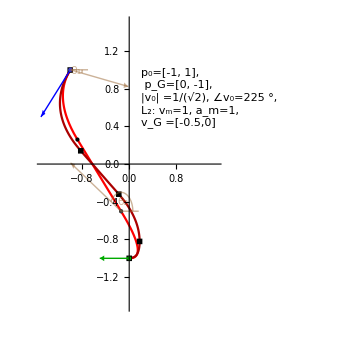
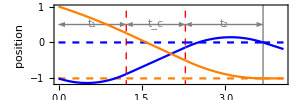
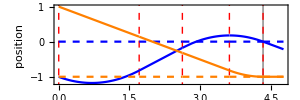
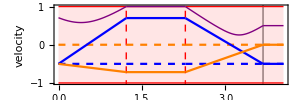
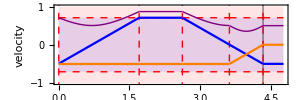
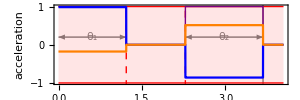
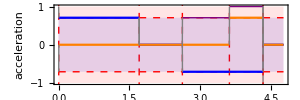
-Graphics- | L_2 Profiles | L_∞ Profiles
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Module[{tMax,pPlot,vPlot,aPlot,stPts,tMaxL2,pPlotL2,vPlotL2,aPlotL2,p0,pV,pG,pGv,mA,mV,tMaxLInf,pPlotLInf,vPlotLInf,aPlotLInf,profilePlots,trajPlotL2,plotRange,trajPlotLInf,trajPlotGraphics,figs,v0,vG,v0Dir,angD,v0Mag,ang,figsCol,LInfSwitchPoints},

p0  ={-1,1};
v0Mag = Norm[{1/2,1/2}];
(*v0Mag = mV/N[Sqrt[2]];*)(*from previous example*)
ang = 225 Degree;
v0Dir = {Cos[ang], Sin[ang]};
pG = {0,-1};
vG = {-.5,0};(*vG = {-0.5,-0};*)
angD = -135;

mA=1;
mV = 1;
(*pGv = {0,-1};*) (* should evaluate to pG for stop at goal *) 
pGv = vG + pG; 
(*pV= {-1.5,.5};*)
pV = N[v0Mag]*v0Dir + p0;
(*No coast, stops at goal*)
plotRange = {{-1.5,1.5},{-1.5,1.5}} ;

{trajPlotL2,tMaxL2,pPlotL2,vPlotL2,aPlotL2}=getL2TrajAndProfiles[p0,pV,pG,pGv,mA,mV,plotRange];
{trajPlotLInf,tMaxLInf,pPlotLInf,vPlotLInf,aPlotLInf,LInfSwitchPoints}=getLInfTrajAndProfiles[p0,pV,pG,pGv,mA,mV];
profilePlots = Multicolumn[{Style["L_2 Profiles" ,FontFamily->"Arial"],pPlotL2,vPlotL2,aPlotL2,Style["L_∞ Profiles" ,FontFamily->"Arial"],pPlotLInf,vPlotLInf,aPlotLInf},{4,2},Alignment->Center];
figs = Show[trajPlotL2,trajPlotLInf,LInfSwitchPoints,Graphics[Text[StringForm["p_0=[``, ``],
 p_G=[``, ``], 
|v_0| =``, ∠v_0=``, 
L_2: v_m=``, a_m=``, 
v_G =[``,``]",p0⟦1⟧,p0⟦2⟧,pG⟦1⟧,pG⟦2⟧,v0Mag, ang,mV,mA, vG⟦1⟧,vG⟦2⟧],{0.2,0.7},{Left,Center}]],ImageSize ->340];
Multicolumn[{figs,profilePlots},{1,2}]
]
```

## Initialization code for L2 path

```mathematica
vanDerCorput[n_,base_:2]:=Table[FromDigits[{Reverse[IntegerDigits[k,base]],0},base],{k,n}] (*https://rosettacode.org/wiki/Van_der_Corput_sequence#Mathematica/Wolfram_Language*)

computeError3Step[p0_,v0_,pG_,vG_,θ1_,θ3_,mA_,mV_]:=Module[{t1,t2,t3,tf,pGest,vGest},
{t1,t2,t3} = calctmVV[p0,pG,v0,vG,mA,mV,θ1,θ3];
tf = t1+t2+t3;
pGest = posVV[tf,p0,v0,mA,mV,θ1,θ3,{t1,t2,t3}];
vGest =velVV[tf,p0,v0,mA,mV,θ1,θ3,{t1,t2,t3}];
(*Print[StringForm["PosErr = ``, VelErr = ``, ",pGest-pG,vGest-vG]];*)
(*(pGest-pG)^2+(vGest-vG)^2*)
Norm[(pGest-pG)]+Norm[(vGest-vG)]
]

numSolveStartAndEndVelCoastTANequation[{p0x_,p0y_},{pGx_,pGy_},{v0x_,v0y_},{vGx_,vGy_},mA_,mV_ ,sval_:0]:=
Module[{ansFR,θ1o,θ3o,vxC,vyC,ϕ},(* ϕ == ArcTan[(pxtm3-pxt1),(pytm3-pyt1)]*)
ansFR=FindRoot[
ϕ==ArcTan[-2 mA (p0x-pGx)-v0x √((v0x-mV Cos[ϕ])^2+(v0y-mV Sin[ϕ])^2)-vGx √((vGx-mV Cos[ϕ])^2+(vGy-mV Sin[ϕ])^2)-mV Cos[ϕ] (√((v0x-mV Cos[ϕ])^2+(v0y-mV Sin[ϕ])^2)+√((vGx-mV Cos[ϕ])^2+(vGy-mV Sin[ϕ])^2)),-2 mA (p0y-pGy)-v0y √((v0x-mV Cos[ϕ])^2+(v0y-mV Sin[ϕ])^2)-vGy √((vGx-mV Cos[ϕ])^2+(vGy-mV Sin[ϕ])^2)-mV Sin[ϕ] (√((v0x-mV Cos[ϕ])^2+(v0y-mV Sin[ϕ])^2)+√((vGx-mV Cos[ϕ])^2+(vGy-mV Sin[ϕ])^2))],  
{ϕ,sval}];
vxC=mV*Cos[ϕ]/.ansFR;
vyC=mV*Sin[ϕ]/.ansFR;
θ1o=ArcTan[vxC-v0x,vyC-v0y];
θ3o=ArcTan[vGx-vxC,vGy-vyC];
{θ1o,θ3o}
]

convertToFindAnalytical[p0_,pG_,v0_,mA_,mV_]:=Module[{θTrans,p0Trans,ϕ, θs,vx0Trans,p0TransRot,solθ,maxError,sError},
(* Finds the orientation to accelerate in so that the system will be able to (eventually) brake to stop at pG.
Inputs: initial position p0, goal position pG, and initial velocity v0, and velocity bound mV and acceleration bound mA.
Returns: solθ, the angle we should apply maximum acceleration in. *)
(*translate so pG is at {0,0}.*)
p0Trans = p0-pG;
vx0Trans =√(v0⟦1⟧^2+v0⟦2⟧^2) ;
(*Print[{N[p0TransRot],vx0Trans,mA,mV}];*)
If[vx0Trans==0,(*Special case: 0 velocity *)
solθ=ArcTan[-p0Trans⟦1⟧,-p0Trans⟦2⟧],
(*rotate so velocity points along x-axis*)
ϕ = -ArcTan[v0⟦1⟧,v0⟦2⟧];
p0TransRot = {
Cos[ϕ]*p0Trans⟦1⟧-Sin[ϕ]*p0Trans⟦2⟧,
 Sin[ϕ]*p0Trans⟦1⟧+Cos[ϕ]*p0Trans⟦2⟧};
If[p0TransRot⟦2⟧==0  (*Special case: the velocity points toward or away from the goal*) ,
θTrans= {0,π },
θTrans=Flatten[analyticalSolutionsθ[N[p0TransRot],N[vx0Trans],N[mA],N[mV]]]
];
(*θTrans=Flatten[analyticalSolutionsθ[N[p0TransRot],N[vx0Trans],N[mA],N[mV]]];*)
(*θTrans= Flatten[analyticalSolutionsθ[p0TransRot,vx0Trans,mA,mV]];*)
(*see if any solutions work.  If so, rotate solutions back to original heading*)
(*Print[{ϕ,θTrans}];*)
maxError = 1000;
solθ = θTrans⟦1⟧;
Table[sError=AnalyticalSolError[p0,pG,v0,mA,mV,Re[θ-ϕ]];
 If[sError<maxError,
maxError=sError;
 solθ=θ-ϕ (*rotate the angle into the original coordinate frame.*)
],{θ,θTrans}];
solθ
]]

AnalyticalSolError[p0_,pG_,v0_,mA_,mV_,θ_]:=Module[{vt1,pt1},
(*given the angle θ, see if at time t1 the velocity lines up with the position error*)
pt1=posT1[θ,p0,v0,mA,mV];
vt1=velT1[θ,p0,v0,mA,mV];
Re[(ArcTan[vt1⟦1⟧,vt1⟦2⟧]-ArcTan[pG⟦1⟧-pt1⟦1⟧,pG⟦2⟧-pt1⟦2⟧])^2]
]


analyticalSolutionsθ[{px0_,py0_},vx0_,mA_,mV_]:=Module[
(*given an initial position {px0,py0} and a goal position of {0,0}, and initial velocity is only in vx0 direction, determines what angle we should apply acceleration mA in so we can eventually brake and stop at {0,0}.  
This requires mV so that we know when we will need to brake.
*)
{sθpc,sθnc,θs,nRoots,
c6,c5,c4,c3,c2,c1,c0},
c0 = Chop[16 mA^4 mV^4 py0^4];c1 =Chop[64 mA^3 mV^4 py0^3 vx0^2] ;c2=Chop[(-32 mA^4 mV^4 px0^2 py0^2-32 mA^4 mV^4 py0^4-8 mA^2 mV^6 py0^2 vx0^2-32 mA^4 mV^2 px0^2 py0^2 vx0^2-32 mA^4 mV^2 py0^4 vx0^2+80 mA^2 mV^4 py0^2 vx0^4-8 mA^2 mV^2 py0^2 vx0^6)] ;

c3=Chop[(-96 mA^3 mV^4 py0^3 vx0^2-16 mA mV^6 py0 vx0^4-96 mA^3 mV^2 py0^3 vx0^4+32 mA mV^4 py0 vx0^6-16 mA mV^2 py0 vx0^8) ];c4=Chop[(16 mA^4 mV^4 px0^4+32 mA^4 mV^4 px0^2 py0^2+16 mA^4 mV^4 py0^4-8 mA^2 mV^6 px0^2 vx0^2-32 mA^4 mV^2 px0^4 vx0^2+8 mA^2 mV^6 py0^2 vx0^2+32 mA^4 mV^2 py0^4 vx0^2+mV^8 vx0^4+8 mA^2 mV^4 px0^2 vx0^4+16 mA^4 px0^4 vx0^4-72 mA^2 mV^4 py0^2 vx0^4+32 mA^4 px0^2 py0^2 vx0^4+16 mA^4 py0^4 vx0^4-4 mV^6 vx0^6+8 mA^2 mV^2 px0^2 vx0^6-72 mA^2 mV^2 py0^2 vx0^6+6 mV^4 vx0^8-8 mA^2 px0^2 vx0^8+8 mA^2 py0^2 vx0^8-4 mV^2 vx0^10+vx0^12) ];c5=Chop[(32 mA^3 mV^4 px0^2 py0 vx0^2+32 mA^3 mV^4 py0^3 vx0^2+8 mA mV^6 py0 vx0^4-64 mA^3 mV^2 px0^2 py0 vx0^4+64 mA^3 mV^2 py0^3 vx0^4-8 mA mV^4 py0 vx0^6+32 mA^3 px0^2 py0 vx0^6+32 mA^3 py0^3 vx0^6-8 mA mV^2 py0 vx0^8+8 mA py0 vx0^10) ];c6=Chop[(16 mA^2 mV^4 px0^2 vx0^4+16 mA^2 mV^4 py0^2 vx0^4-32 mA^2 mV^2 px0^2 vx0^6+32 mA^2 mV^2 py0^2 vx0^6+16 mA^2 px0^2 vx0^8+16 mA^2 py0^2 vx0^8) ];
If[c6≠0,nRoots=6,
If[c5 ≠ 0,nRoots=5,
If[c4≠0,nRoots=4,
If[c3≠ 0,nRoots = 3,
If[c2 ≠ 0,nRoots=2,
If[c1≠0,nRoots=1]]]]]];
sθpc=Table[Root[c0+c1 #1+c2  #1^2+c3  #1^3+c4  #1^4+c5  #1^5+c6  #1^6&,k],{k,1,nRoots}];
(*Are the last 2 roots always imaginary? That's why I'm only picking the first 4... is that justifiable? No: we must check all 6.  When the solution is very close they are not all imaginary.

However, sometimes there aren't 6 roots, for instance with final velocity 0.  Can I ask for all that exist?
I think this only happens when you are perpendicular to the v0 vector, on the line at -v0

*)
(*the negative Cosine[θ] solutions are exactly the same.  Weird. *)
(*sθnc=Table[Root[vx0^4 (-mV^2+vx0^2)^4 #1^4+8 mA py0 vx0^4 (mV^2-vx0^2)^2 #1^3 (-2 mV^2+(mV^2+vx0^2) #1^2)+32 mA^3 py0 vx0^2 #1 (2 mV^4 py0^2-3 mV^2 py0^2 (mV^2+vx0^2) #1^2+(mV^4 (px0^2+py0^2)+2 mV^2 (-px0^2+py0^2) vx0^2+(px0^2+py0^2) vx0^4) #1^4)+8 mA^2 vx0^2 #1^2 (-mV^2 py0^2 (mV^4-10 mV^2 vx0^2+vx0^4)+(mV^2+vx0^2) (mV^4 (-px0^2+py0^2)+2 mV^2 (px0^2-5 py0^2) vx0^2+(-px0^2+py0^2) vx0^4) #1^2+2 vx0^2 (mV^4 (px0^2+py0^2)+2 mV^2 (-px0^2+py0^2) vx0^2+(px0^2+py0^2) vx0^4) #1^4)+16 mA^4 ((px0^2+py0^2)^2 vx0^4 #1^4+mV^4 (py0^2-(px0^2+py0^2) #1^2)^2-2 mV^2 vx0^2 #1^2 (py0^2 (px0^2+py0^2)+(px0^4-py0^4) #1^2))&,k],{k,1,6}];*)
(*θs =Join[Table[ArcTan[√(1- sθ^2),sθ],{sθ,sθpc}],Table[ArcTan[-√(1- sθ^2),sθ],{sθ,sθnc}]]*)
θs =Join[Table[ArcTan[√(1- sθ^2),sθ],{sθ,sθpc}],Table[ArcTan[-√(1- sθ^2),sθ],{sθ,sθpc}]]
]


totalTime[t1_,θ_,p0_,pG_,v0_,mA_,mV_]:=Module[{t2, r,d,t3,posDIFFt1},
r = mV^2/(2 mA); (*Radius of braking circle*)
posDIFFt1 = pG-(p0+t1*v0+mA/2*({{Cos[θ]}, {Sin[θ]}})*t1^2);
d = Norm[posDIFFt1];
t2 = (d-r)/mV;(*coasting time*)
t3 = mV/mA;(*braking time*)
t1+t2+t3
]


posT1[θ_,p0_,v0_,mA_,mV_]:=Module[{t1,pt1}, (*Position where particle reaches maxVelocity under maximum accleration in direction θ*)
t1 =computet1[θ,v0,mA,mV];
pt1=Flatten[p0+t1*v0+mA/2*({{Cos[θ]}, {Sin[θ]}})*t1^2]]

velT1[θ_,p0_,v0_,mA_,mV_]:=Module[{t1,vt1},(*Velocity when particle reaches maxVelocity under maximum accleration in direction θ*)
t1 =computet1[θ,v0,mA,mV];
vt1=Flatten[(v0+({{Cos[θ]}, {Sin[θ]}})*t1*mA)]]

computet1[θ_,v0_,mA_,mV_]:=Module[{t1,vx0,vy0}, (*If the particle is moved with maximum acceleration in direction θ until max velocity is achieved, t1 is when the particle speed is mV.  s default to +1, the positive root*)
{vx0,vy0}=v0;
t1=(-(vx0 Cos[θ]+vy0 Sin[θ])+√(mV^2-vx0^2-vy0^2+(vx0 Cos[θ]+vy0 Sin[θ])^2))/mA] 

pos[t_,t1_,θ_,p0_,pG_,v0_,mA_,mV_]:=Module[{t2, r,d,t3,posDIFFt1},
r = mV^2/(2 mA); (*Radius of braking circle*)
posDIFFt1 = pG-(p0+t1*v0+mA/2*({{Cos[θ]}, {Sin[θ]}})*t1^2);
d = Norm[posDIFFt1];
t2 = (d-r)/mV;(*coasting time*)
t3 = mV/mA;(*braking time*)
Flatten[p0+t*v0+Piecewise[{{mA/2*({{Cos[θ]}, {Sin[θ]}})*t^2, t<t1}, {mA/2*({{Cos[θ]}, {Sin[θ]}})*t1^2+(t-t1)*(({{Cos[θ]}, {Sin[θ]}})*t1*mA), t<t1+t2}, {mA/2*({{Cos[θ]}, {Sin[θ]}})*t1^2+(t-t1)*(({{Cos[θ]}, {Sin[θ]}})*t1*mA)+mA/2*(t-t1-t2)^2(-posDIFFt1/d), t<t1+t2+t3}, {-t*v0+pG-p0, True}}]]]
vel[t_,t1_,θ_,p0_,pG_,v0_,mA_,mV_]:=Module[{t2, r,d,t3,posDIFFt1},
r = mV^2/(2 mA); (*Radius of braking circle*)
posDIFFt1 = pG-(p0+t1*v0+mA/2*({{Cos[θ]}, {Sin[θ]}})*t1^2);
d = Norm[posDIFFt1];
 t2 = (d-r)/mV;(*coasting time*)
t3 = mV/mA;(*braking time*)
Flatten[v0+Piecewise[{{mA*({{Cos[θ]}, {Sin[θ]}})*t, t<t1}, {mA*({{Cos[θ]}, {Sin[θ]}})*t1, t<t1+t2}, {mA*({{Cos[θ]}, {Sin[θ]}})*t1+mA*(t-t1-t2)(-posDIFFt1/d), t<t1+t2+t3}, {-v0, True}}]]]
acc[t_,t1_,θ_,p0_,pG_,v0_,mA_,mV_]:=Module[{t2, r,d,t3,posDIFFt1},
r = mV^2/(2 mA); (*Radius of braking circle*)
posDIFFt1 = pG-(p0+t1*v0+mA/2*({{Cos[θ]}, {Sin[θ]}})*t1^2);
d = Norm[posDIFFt1];
 t2 = (d-r)/mV;(*coasting time*)
t3 = mV/mA;(*braking time*)
Flatten[Piecewise[{{mA*({{Cos[θ]}, {Sin[θ]}}), t<t1}, {({{0}, {0}}), t<t1+t2}, {mA*(-posDIFFt1/d), t<t1+t2+t3}, {({{0}, {0}}), True}}]]]
(*numSolveStartAndEndVel[p0,pG,v0,vG,mA,mV,3];(*t,τ,θ,ϕ*)*)
numSolveStartAndEndVel2[p0_,pG_,v0_,vG_,mA_,mV_,iterations_:1,ϕ_]:=Module[{θ1,pT1,θ2,pT2,pS1,pS2,err,iter=0,t1,t2,t3},
(*Returns {θ1,θ2}, the angles for the two bang bang inputs. The system coasts in between.  This version starts with a guess for the angle ϕ at the end when starting from pG with velocity -vG. ϕ should be calculated using the no-coasting assumption.
*)
(*pS1 = p0+Norm[v0]^2/(2 mA)Normalize[v0];(*Stopping point with full braking starting at p0*)
pS2 = pG-Norm[vG]^2/(2 mA)Normalize[vG]; (*Stopping point with full braking starting at pG, back in time*)
pT2 =1/2(pS1+pS2)(*+mV^2/(2 mA)Normalize[pS2-pS1]*)(*+Norm[-vG+v0]^2/(2 mA)Normalize[-vG+v0]*);*)
(*Start pT2 at midpoint of stop, accelerate, stop path*)
pT2 =posT1[ϕ,pG,-vG,mA,mV];(*end of coasting position*)
err = 10;
While[err>0.001 && iter <11,
θ1 = convertToFindAnalytical[p0,pT2,v0,mA,mV]; (*Pick θ1 to start at {p0, v0}, finishes at pT2 *)
pT1 =posT1[θ1,p0,v0,mA,mV]; (*start of coasting position*)
θ2 = convertToFindAnalytical[pG,pT1,-vG,mA,mV]; (*Pick θ2 go back in time from {pG,vG} reaches pT1 *)
pT2 =posT1[θ2,pG,-vG,mA,mV];(*end of coasting position*)

(*Calculate the error*)
iter = iter+1;
{t1,t2,t3} = calctmVV[p0,pG,v0,vG,mA,mV,θ1,θ2];

err = Norm[posVV[t1+t2+t3,p0,v0,mA,mV,θ1,θ2,{t1,t2,t3}]-pG];
(*Print[StringForm["iter=``,err = ``",iter,err]];*)
];
(*Print[iter];*)
{θ1,θ2}
]


numSolveStartAndEndVel[p0_,pG_,v0_,vG_,mA_,mV_,iterations_:1]:=Module[{θ1,pT1,θ2,pT2,pS1,pS2},
(*Returns {θ1,θ2}, the angles for the two bang bang inputs. The system coasts in between.*)
(*pT2 =pG-vG; (*Start  pT2 at pG-vG*)*)
pS1 = p0+Norm[v0]^2/(2 mA)Normalize[v0];(*Stopping point with full braking starting at p0*)
pS2 = pG-Norm[vG]^2/(2 mA)Normalize[vG]; (*Stopping point with full braking starting at pG, back in time*)
pT2 =1/2(pS1+pS2)(*+mV^2/(2 mA)Normalize[pS2-pS1]*)(*+Norm[-vG+v0]^2/(2 mA)Normalize[-vG+v0]*);
(*Start pT2 at midpoint of stop, accelerate, stop path*)
pT2 =pG-vG;
Table[
θ1 = convertToFindAnalytical[p0,pT2,v0,mA,mV]; (*Pick θ1 to start at {p0, v0}, finishes at pT2 *)
pT1 =posT1[θ1,p0,v0,mA,mV]; (*start of coasting position*)
θ2 = convertToFindAnalytical[pG,pT1,-vG,mA,mV]; (*Pick θ2 go back in time from {pG,vG} reaches pT1 *)
pT2 =posT1[θ2,pG,-vG,mA,mV];(*end of coasting position*)
,{i,iterations}];
{θ1,θ2}
]

changeCoordinates[p0_,pG_,v0_,vG_,mA_,mV_]:=Module[{p0Trans,vx0Trans,ϕ ,rotϕ,p0TransRot},
(*translate so pG is at {0,0}*)
p0Trans = p0-pG;
vx0Trans =√(v0⟦1⟧^2+v0⟦2⟧^2) ;
ϕ =If[vx0Trans==0,(*Special case: 0 velocity *) 0, -ArcTan[v0⟦1⟧,v0⟦2⟧]]; 
(*rotate so velocity points along x-axis*)
rotϕ = {
{Cos[ϕ],-Sin[ϕ]},
{ Sin[ϕ],+Cos[ϕ]}};
p0TransRot = rotϕ.p0Trans;
(*{p0,pG,v0,vG,ϕ }*)
{p0TransRot,{0,0},{vx0Trans,0}, rotϕ.vG,ϕ }
]

numSolveBBStartAndEndVel[p0_,pG_,v0_,vG_,mA_]:=Module[{midPt,
solt1,solθ1,maxV1, tMax1,solt2,solθ2,maxV2, tMax2,ansFR,p0x,p0y,v0x,v0y,vGx, vGy,pGx,pGy,t1,t2,θ1,θ2},
(*Returns the bang-bang solution (no coasting phase) with the two pairs of angles and times for thrusting:
{t1,θ1,t2,θ2}*)
(*midPt = (p0+v0 /mA +pG -vG/mA)/2; (*TODO: switch to better midpoint*)*)
midPt =(p0+Normalize[v0]Norm[v0]^2 /mA +pG -Normalize[vG]Norm[vG]^2 /mA )/2;
{solt1,solθ1,{maxV1, tMax1}}=findAccelSolAna[p0,midPt,v0,mA];
Print[StringForm["{solt1,solθ1,{maxV1, tMax1}}=``",{solt1,solθ1,{maxV1, tMax1}}]];
{solt2,solθ2,{maxV2, tMax2}}=findAccelSolAna[p0,midPt,-vG,mA];
Print[StringForm["{solt2,solθ2,{maxV2, tMax2}}=``",{solt2,solθ2,{maxV2, tMax2}}]];
{p0x,p0y}= p0;
{v0x,v0y}=v0;
{pGx, pGy}=pG;
{vGx, vGy}=vG;
ansFR=FindRoot[
{   p0x+v0x*t1+mA/2 Cos[θ1] t1^2==pGx-vGx*t2+mA/2Cos[θ2] t2^2&&
p0y+v0y*t1+mA/2Sin[θ1] t1^2==pGy-vGy*t2+mA/2Sin[θ2] t2^2&&
v0x + mA*Cos[θ1]t1==vGx -  mA*Cos[θ2]t2&&
v0y + mA*Sin[θ1]t1==vGy -  mA*Sin[θ2]t2}, {{t1,solt1},{t2,solt2},{θ1,solθ1},{θ2,solθ2}}];
Print[StringForm["The error is ``",computeErr[p0,pG,v0,vG,t1,t2,θ1,θ2,mA]/.ansFR]];
{t1,θ1,t2,θ2}/.ansFR   (*incorporate the error term*)
]

(*numSolveBBStartAndEndVel[p0i_,pGi_,v0i_,vGi_,mA_,mVi_]:=Module[{midPt,p0,pG,v0,vG,ϕ,
solt1,solθ1,maxV1, tMax1,solt2,solθ2,maxV2, tMax2,ansFR,p0x,p0y,v0x,vGx, vGy,t1,t2,θ1,θ2,mV},
mV = 100;
(*Returns the bang-bang solution (no coasting phase) with the two pairs of angles and times for thrusting:
{t1,θ1,t2,θ2}
*)
{p0,pG,v0,vG,ϕ }=changeCoordinates[p0i,pGi,v0i,vGi,mA,mV];
midPt = (p0+v0 /mA +pG -vG)/2; (*TODO: switch to better midpoint*)
{solt1,solθ1,{maxV1, tMax1}}=findAccelSolAna[p0,midPt,v0,mA];
Print[StringForm["{solt1,solθ1,{maxV1, tMax1}}=``",{solt1,solθ1,{maxV1, tMax1}}]];
{solt2,solθ2,{maxV2, tMax2}}=findAccelSolAna[p0,midPt,-vG,mA];
Print[StringForm["{solt2,solθ2,{maxV2, tMax2}}=``",{solt2,solθ2,{maxV2, tMax2}}]];
{p0x,p0y} = p0;
v0x = v0⟦1⟧;
{vGx, vGy}=vG;
ansFR=FindRoot[
{p0x+v0x*t1+1/2 Cos[θ1] t1^2==-vGx*t2+1/2Cos[θ2] t2^2&&
p0y+1/2Sin[θ1] t1^2==-vGy*t2+1/2Sin[θ2] t2^2&&
v0x +  Cos[θ1]t1==vGx -  Cos[θ2]t2&&
 Sin[θ1]t1==vGy -  Sin[θ2]t2}, {{t1,solt1},{t2,solt2},{θ1,solθ1},{θ2,solθ2}}];
Print[StringForm["The error is ``",computeErr[{p0x,p0y},{0,0},v0x,{vGx,vGy},t1,t2,θ1,θ2]/.ansFR]];
{t1,θ1-ϕ,t2,θ2-ϕ}/.ansFR   (*incorporate the error term*)

]*)

drawRocketThrust[pt_,at_]:=Module[{nat},
nat=Norm[at];
{EdgeForm[None],If[at≠ {0,0}, Rotate[{   (*This is wrong, since it allows us to rotate the thrust*)
Red,        Disk[pt-{.2+nat,0},1.00nat{1,.2}],
Orange ,Disk[pt-{.2+.75nat,0},0.75nat{1,.2}],
Yellow ,Disk[pt-{.2+.4nat,0},0.40nat{1,.2}]},ArcTan[First@at,Last@at],pt]],
Gray,Disk[pt,0.3]
}
]

posAndtAtt1[θ_,p0_,v0_,mA_,mV_]:=Module[{t1,pt1}, (*returns {Position,time} where & when particle reaches maxVelocity under maximum accleration in direction θ*)
t1 =computet1[θ,v0,mA,mV];
pt1=Flatten[p0+t1*v0+mA/2*({{Cos[θ]}, {Sin[θ]}})*t1^2];
{t1,pt1}
]

(*Start and stop velocity*)
calctmVV[p0_,pG_,v0_,vG_,mA_,mV_,θ1_,θ2_]:=Module[{t1,pt1,t2,t3,pt3},
{t1, pt1}=posAndtAtt1[θ1,p0,v0,mA,mV];
{t3, pt3}=posAndtAtt1[θ2,pG,-vG,mA,mV];
t2 = Norm[pt1-pt3]/mV;
Chop[{t1,t2,t3}]
]

posVV[t_,p0_,v0_,mA_,mV_,θ1_,θ2_,{t1_,t2_,t3_}]:=
Flatten[p0+t*v0+Piecewise[{{mA/2*({{Cos[θ1]}, {Sin[θ1]}})*t^2, t<t1}, {mA/2*({{Cos[θ1]}, {Sin[θ1]}})*t1^2+(t-t1)*(({{Cos[θ1]}, {Sin[θ1]}})*t1*mA), t<t1+t2}, {mA/2*({{Cos[θ1]}, {Sin[θ1]}})*t1^2+(t-t1)*(({{Cos[θ1]}, {Sin[θ1]}})*t1*mA)+mA/2*(t-t1-t2)^2({{Cos[θ2]}, {Sin[θ2]}}), t<t1+t2+t3}, {mA/2*({{Cos[θ1]}, {Sin[θ1]}})*t1^2+(t-t1)*(({{Cos[θ1]}, {Sin[θ1]}})*t1*mA)+mA/2*(t3)^2({{Cos[θ2]}, {Sin[θ2]}})+(t-t1-t2-t3)*(({{Cos[θ2]}, {Sin[θ2]}})*t3*mA), True}}]]
velVV[t_,p0_,v0_,mA_,mV_,θ1_,θ2_,{t1_,t2_,t3_}]:=
Flatten[v0+Piecewise[{{mA*({{Cos[θ1]}, {Sin[θ1]}})*t, t<t1}, {mA*({{Cos[θ1]}, {Sin[θ1]}})*t1, t<t1+t2}, {mA*({{Cos[θ1]}, {Sin[θ1]}})*t1+mA*(t-t1-t2)({{Cos[θ2]}, {Sin[θ2]}}), t<t1+t2+t3}, {mA*({{Cos[θ1]}, {Sin[θ1]}})*t1+mA*({{Cos[θ2]}, {Sin[θ2]}})*t3, True}}]]

velVV2[t_,p0_,v0_,mA_,mV_,θ1_,θ2_,{t1_,t2_,t3_}]:=
Flatten[v0+Piecewise[{{mA*({{Cos[θ1]}, {Sin[θ1]}})*t, 0≤ t<t1}, {mA*({{Cos[θ1]}, {Sin[θ1]}})*t1, t1≤ t<t1+t2}, {mA*({{Cos[θ1]}, {Sin[θ1]}})*t1+mA*(t-t1-t2)({{Cos[θ2]}, {Sin[θ2]}}), t1+t2≤ t}}]]

velVV2x[t_,p0_,v0_,mA_,mV_,θ1_,θ2_,{t1_,t2_,t3_}]:=

v0[[1]]+Piecewise[{{mA*Cos[θ1]*t, 0≤ t<t1}, {mA*Cos[θ1]*t1, t1≤ t<t1+t2}, {mA*Cos[θ1]*t1+mA*(t-t1-t2)Cos[θ2], t1+t2≤ t}}]

velVV2y[t_,p0_,v0_,mA_,mV_,θ1_,θ2_,{t1_,t2_,t3_}]:=

v0[[2]]+Piecewise[{{mA*Sin[θ1]*t, 0≤ t<t1}, {mA*Sin[θ1]*t1, t1≤ t<t1+t2}, {mA*Sin[θ1]*t1+mA*(t-t1-t2)Sin[θ2], t1+t2≤ t}}]



accVV[t_,p0_,v0_,mA_,mV_,θ1_,θ2_,{t1_,t2_,t3_}]:=
Flatten[Piecewise[{{mA*({{Cos[θ1]}, {Sin[θ1]}}), t<t1}, {({{0}, {0}}), t<t1+t2}, {mA*({{Cos[θ2]}, {Sin[θ2]}}), t<t1+t2+t3}, {({{0}, {0}}), True}}]]


posBB[t_,t1_,θ1_,p0_,pG_,v0_,mA_]:=Module[{t2,vt1},
vt1 = v0+{Cos[θ1],Sin[θ1]}t1 mA;
t2 = Norm[vt1]/mA;(*braking time*)
p0+t*v0+Piecewise[{{mA/2*{Cos[θ1],Sin[θ1]}*t^2, t≤ t1}, {mA/2*{Cos[θ1],Sin[θ1]}*t1^2+(t-t1)*({Cos[θ1],Sin[θ1]}*t1*mA)-(t-t1)^2 mA/2 Normalize[vt1], t<t1+t2}, {-t*v0+pG-p0, True}}]]

velBB[t_,t1_,θ1_,p0_,pG_,v0_,mA_]:=Module[{t2,vt1},
vt1 = v0+{Cos[θ1],Sin[θ1]}t1 mA;
t2 = Norm[vt1]/mA;(*braking time*)
Piecewise[{{v0+mA*{Cos[θ1],Sin[θ1]}*t, t≤ t1}, {v0+mA*{Cos[θ1],Sin[θ1]}*t1-(t-t1)mA Normalize[vt1], t<t1+t2}, {{0,0}, True}}]]
accBB[t_,t1_,θ1_,p0_,pG_,v0_,mA_]:=Module[{t2,vt1},
vt1 = v0+{Cos[θ1],Sin[θ1]}t1 mA;
t2 = Norm[vt1]/mA;(*braking time*)
Piecewise[{{mA{Cos[θ1],Sin[θ1]}, t≤ t1}, {-mA Normalize[vt1], t<t1+t2}, {{0,0}, True}}]]

posT1plus[θ_,p0_,v0_,mA_,mV_]:=Module[{t1,pt,v0x,v0y}, (*Position where particle reaches maxVelocity under maximum accleration in direction θ*)
t1 =computet1[θ,v0,mA,mV]; (* v(t1) = {v0x,v0y}+mA*{Cos[θ],Sin[θ]}*t1,  time to stop is mV/mA *)
(*pt1=p0+t1*v0+mA/2*{Cos[θ],Sin[θ]}*t1^2+1/2 mV^2/mA Normalize[v0+mA*{Cos[θ],Sin[θ]}*t1]]*)
{v0x,v0y} = v0;
pt=p0+t1*{v0x,v0y}+mA/2*{Cos[θ],Sin[θ]}*t1^2+ {(v0x+mA t1 Cos[θ]) ,(v0y+mA t1 Sin[θ])}1/(2 mA)( √((v0x+mA t1 Cos[θ])^2+(v0y+mA t1 Sin[θ])^2))
]

posStop[p0_,{v0x_,v0y_},mA_,t_,θ_]:=p0+t*{v0x,v0y}+mA/2*{Cos[θ],Sin[θ]}*t^2+ {(v0x+mA t Cos[θ]) ,(v0y+mA t Sin[θ])}1/(2 mA)( √((v0x+mA t Cos[θ])^2+(v0y+mA t Sin[θ])^2));
velAndTotalTimeBB[t1_,θ1_,v0_,mA_]:=Module[{t2,vt1,nVt1},
(*Given an system with initial velocity v0 that applies max acceleration mA in direction θ1 for t1, calculates the velocity at time t1 and the time required to stop the particle.*)
vt1 = v0+{Cos[θ1],Sin[θ1]}t1 mA;
t2 = Norm[vt1]/mA;(*braking time*)
{vt1,t1+t2}
]

findAccelSolAna[p0_,pG_,v0_,mA_]:=Module[{θTrans,p0Trans,ϕ, θs,v0x,p0TransRot,maxError,sError,p0x,p0y,myt,c1,solt,solθ,maxErr,derror, nRoots,e0,e1,e2,e3,e4,e5,e6,kbest=0},
(*  A bang-bang controller to stop at point pG, if you start at p0 with Velocity v0.
returns solt, the time (in seconds) to apply max thrust at angle solθ (immediately followed by breaking at maximum acceleration mA).
{solt,solθ,{max velocity, total time}}
{solt,solθ,velAndTotalTimeBB[solt,solθ,v0,mA]}
*)
(*  (*This equation is the result of maximum braking starting at time t, and determining the halting position.  We want to stop at {0,0}.*)
sol = Solve[{2p0x+2t v0x+ t^2 c1+ (v0x+t c1) √(t^2+v0x^2+2 t v0x c1)==0,2 p0y+t (t+√(t^2+v0x^2+2 t v0x c1)) √(1- c1^2)==0},{t,c1}]
(*This gives 6 ugly solutions. √(1+ c1^2) is other 6.  The t is relatively simple.  The c1 is not.  The c1 is composed of the answer to t 3x, so we can simplify it, as shown below.*)
*)
(*translate so pG is at {0,0}*)
p0Trans = p0-pG;
v0x =√(v0⟦1⟧^2+v0⟦2⟧^2) ;
If[v0x==0,(*Special case: 0 velocity *)
solt = (√(p0Trans⟦1⟧^2+p0Trans⟦2⟧^2))/mA;
{solt,ArcTan[-p0Trans⟦1⟧,-p0Trans⟦2⟧],{solt*mA,2solt}}
,
(*rotate coordinate frame so velocity points along x-axis*)
ϕ = -ArcTan[v0⟦1⟧,v0⟦2⟧];
{p0x,p0y} = {
Cos[ϕ]*p0Trans⟦1⟧-Sin[ϕ]*p0Trans⟦2⟧,
Sin[ϕ]*p0Trans⟦1⟧+Cos[ϕ]*p0Trans⟦2⟧};
(*remove the mA term*)
{p0x,p0y} = {p0x,p0y}/mA; (*Chop[] forces numbers close to 0 to be 0*)
v0x=v0x/mA;

If[ Abs[p0y] <0.00001,(*Special case: initial velocity points to goal *)
If[p0x<0, (*Two options: either we can go directly to goal, or we overshoot it*)
 solθ =0; solt = Max[(√((-2 p0x+v0x^2)^3))/(√2 (-2 p0x+v0x^2)),(√((-2 p0x+v0x^2)^3))/(√2 (2 p0x-v0x^2))]-v0x;,
solθ =π; solt = Max[-(√((2 p0x+v0x^2)^3))/(√2 (2 p0x+v0x^2)),+(√((2 p0x+v0x^2)^3))/(√2 (2 p0x+v0x^2))]+v0x];
(*Print[StringForm["p0y close to zero, solθ=``, solt = ``",solθ , solt]];*)
,
(*Non-special case*)

maxErr = 100; (*start with a large error.*)
(*the solution for time is the roots of a sextic polynomial*)
(*Calculate the coefficients of the sextic polynomial*)
e0=Chop[-64 p0x^6-192 p0x^4 p0y^2-192 p0x^2 p0y^4-64 p0y^6+32 p0x^4 v0x^4-192 p0x^2 p0y^2 v0x^4+32 p0y^4 v0x^4-4 p0x^2 v0x^8-4 p0y^2 v0x^8];e1=Chop[(-320 p0x^5 v0x-640 p0x^3 p0y^2 v0x-320 p0x p0y^4 v0x+96 p0x^3 v0x^5-288 p0x p0y^2 v0x^5-4 p0x v0x^9)] ;e2=Chop[(-464 p0x^4 v0x^2-672 p0x^2 p0y^2 v0x^2-208 p0y^4 v0x^2+120 p0x^2 v0x^6-88 p0y^2 v0x^6-v0x^10)] ;e3=Chop[(-256 p0x^3 v0x^3-128 p0x p0y^2 v0x^3+64 p0x v0x^7) ];e4=Chop[(64 p0x^4+128 p0x^2 p0y^2+64 p0y^4-64 p0x^2 v0x^4+32 p0y^2 v0x^4+12 v0x^8) ];e5=Chop[(64 p0x^3 v0x+64 p0x p0y^2 v0x-16 p0x v0x^5)] ;
e6=Chop[(16 p0x^2 v0x^2-4 v0x^6)];

If[e6≠0,nRoots=6,  (*determine how many roots exist. If any leading coefficient is zero, that root doesn't exist.*)
If[e5≠ 0,nRoots=5,
If[e4≠0,nRoots=4,
If[e3≠ 0,nRoots = 3,
If[e2 ≠ 0,nRoots=2,
If[e1 ≠0,nRoots=1]]]]]];
Table[
myt =Root[e0+e1#1+e2#1^2+e3 #1^3+e4 #1^4+e5 #1^5+e6#1^6&,k];
If[ myt∈Reals&&myt>0 , (*the time value for our control must be real and be positive. Otherwise, skip it.*)
(*Calculate the cosign for the given t value myt.*)
c1=(4 p0x v0x^2 (-4096 (p0x^2+p0y^2)^5 (15 p0x^4-49 p0x^2 p0y^2+40 p0y^4)+2048 (p0x^2+p0y^2)^2 (49 p0x^8-41 p0x^6 p0y^2-303 p0x^4 p0y^4+529 p0x^2 p0y^6-186 p0y^8) v0x^4-256 (273 p0x^10-28 p0x^8 p0y^2-1114 p0x^6 p0y^4+804 p0x^4 p0y^6-1263 p0x^2 p0y^8+1216 p0y^10) v0x^8+256 (105 p0x^8-183 p0x^6 p0y^2+163 p0x^4 p0y^4-73 p0x^2 p0y^6-220 p0y^8) v0x^12+16 (-385 p0x^6+1278 p0x^4 p0y^2-2233 p0x^2 p0y^4+1192 p0y^6) v0x^16+8 (105 p0x^4-443 p0x^2 p0y^2+542 p0y^4) v0x^20+7 (-9 p0x^2+32 p0y^2) v0x^24+2 v0x^28)+myt (-4096 (p0x^2+p0y^2)^4 (159 p0x^6-344 p0x^4 p0y^2+51 p0x^2 p0y^4+74 p0y^6) v0x^3+2048 (p0x^2+p0y^2) (497 p0x^10-79 p0x^8 p0y^2-1890 p0x^6 p0y^4+1510 p0x^4 p0y^6+673 p0x^2 p0y^8-359 p0y^10) v0x^7-256 (2593 p0x^10-360 p0x^8 p0y^2-7914 p0x^6 p0y^4+6700 p0x^4 p0y^6-2223 p0x^2 p0y^8+1988 p0y^10) v0x^11+256 (905 p0x^8-862 p0x^6 p0y^2-1020 p0x^4 p0y^4+1106 p0x^2 p0y^6-201 p0y^8) v0x^15+16 (-2865 p0x^6+4204 p0x^4 p0y^2-1685 p0x^2 p0y^4+1886 p0y^6) v0x^19+8 (617 p0x^4-966 p0x^2 p0y^2+709 p0y^4) v0x^23+(-239 p0x^2+272 p0y^2) v0x^27+2 v0x^31+myt (8 p0x (-4096 (p0x^2-2 p0y^2) (p0x^2+p0y^2)^6-1024 (p0x^2+p0y^2)^3 (44 p0x^6-81 p0x^4 p0y^2-10 p0x^2 p0y^4+19 p0y^6) v0x^4+256 (299 p0x^10+45 p0x^8 p0y^2-1018 p0x^6 p0y^4+434 p0x^4 p0y^6+559 p0x^2 p0y^8-127 p0y^10) v0x^8-128 (400 p0x^8-317 p0x^6 p0y^2-715 p0x^4 p0y^4+753 p0x^2 p0y^6-17 p0y^8) v0x^12+16 (1125 p0x^6-1602 p0x^4 p0y^2-275 p0x^2 p0y^4+852 p0y^6) v0x^16-4 (884 p0x^4-1401 p0x^2 p0y^2+255 p0y^4) v0x^20+9 (41 p0x^2-47 p0y^2) v0x^24-16 v0x^28)+4 myt v0x (4096 (p0x^2+p0y^2)^5 (4 p0x^4-11 p0x^2 p0y^2+6 p0y^4)-1024 (p0x^2+p0y^2)^2 (45 p0x^8-31 p0x^6 p0y^2-167 p0x^4 p0y^4+219 p0x^2 p0y^6-58 p0y^8) v0x^4+256 (189 p0x^10+6 p0x^8 p0y^2-702 p0x^6 p0y^4+732 p0x^4 p0y^6-359 p0x^2 p0y^8+182 p0y^10) v0x^8-128 (205 p0x^8-217 p0x^6 p0y^2-290 p0x^4 p0y^4+447 p0x^2 p0y^6-109 p0y^8) v0x^12+16 (510 p0x^6-883 p0x^4 p0y^2+255 p0x^2 p0y^4+56 p0y^6) v0x^16-4 (369 p0x^4-681 p0x^2 p0y^2+308 p0y^4) v0x^20+(145 p0x^2-188 p0y^2) v0x^24-6 v0x^28+4 myt p0x v0x (4 (p0x^2+p0y^2)-v0x^4) (512 (p0x^2+p0y^2)^3 (3 p0x^4-7 p0x^2 p0y^2+3 p0y^4)-64 (32 p0x^8-13 p0x^6 p0y^2-119 p0x^4 p0y^4+169 p0x^2 p0y^6-45 p0y^8) v0x^4+16 (68 p0x^6-95 p0x^4 p0y^2-40 p0x^2 p0y^4+75 p0y^6) v0x^8-4 (72 p0x^4-135 p0x^2 p0y^2+61 p0y^4) v0x^12+19 (2 p0x^2-3 p0y^2) v0x^16-2 v0x^20)+myt^2 v0x^2 (-2 p0x+v0x^2) (2 p0x+v0x^2) (-256 (p0x^2+p0y^2)^3 (7 p0x^4-15 p0x^2 p0y^2+6 p0y^4)+128 (18 p0x^8-11 p0x^6 p0y^2-51 p0x^4 p0y^4+83 p0x^2 p0y^6-23 p0y^8) v0x^4-32 (37 p0x^6-59 p0x^4 p0y^2-11 p0x^2 p0y^4+37 p0y^6) v0x^8+8 (38 p0x^4-73 p0x^2 p0y^2+31 p0y^4) v0x^12+(-39 p0x^2+56 p0y^2) v0x^16+2 v0x^20)))))/(8 (4 (p0x^2+p0y^2)-v0x^4) (16 (p0x^2+p0y^2)^3-8 (p0x^4-6 p0x^2 p0y^2+p0y^4) v0x^4+(p0x^2+p0y^2) v0x^8) (64 p0x^8+16 p0x^6 (4 p0y^2+5 v0x^4)-2 (8 p0y^4+10 p0y^2 v0x^4+v0x^8)^2-12 p0x^4 (16 p0y^4+56 p0y^2 v0x^4+7 v0x^8)+p0x^2 (-320 p0y^6+976 p0y^4 v0x^4+324 p0y^2 v0x^8+23 v0x^12)));
θs = ArcTan[c1, √(1-c1^2)]-ϕ ; (*positive sine value.*)
derror= Norm[posStop[p0,v0,mA,myt,θs]-pG];
If[derror<maxErr,maxErr=derror; solt =myt;solθ=θs;kbest=k;
(*If[derror<10.^-9,(*Print[StringForm["k=``,derror=``",k, derror]];*)Return[{solt,solθ,velAndTotalTimeBB[solt,solθ,v0,mA]}];];*)
 ];
θs = ArcTan[c1, -√(1-c1^2)]-ϕ ; (*negative sine value.*)
derror= Norm[posStop[p0,v0,mA,myt,θs]-pG];
If[ derror<maxErr,maxErr=derror; solt =myt;solθ=θs;kbest=k+6;
(*If[derror<10.^-9,(*Print[StringForm["k=``,derror=``",k, derror]];*)Return[{solt,solθ,velAndTotalTimeBB[solt,solθ,v0,mA]}];];*)
 ];
],{k,1,nRoots}]];
{solt,solθ,velAndTotalTimeBB[solt,solθ,v0,mA]}
]]

computeErr[{p0x_,p0y_},{pFx_,pFy_},{v0x_,v0y_},{vFx_,vFy_},t_,τ_,θ_,ϕ_,mA_]:=Module[{pFxG,pFyG ,vFxG,vFyG},
{pFxG,pFyG ,vFxG,vFyG} = computeModel[{p0x,p0y},{v0x,v0y},t,τ,θ,ϕ,mA];
{pFx-pFxG, pFy-pFyG,vFx-vFxG,vFy-vFyG}
]

computeModel[{p0x_,p0y_},{v0x_,v0y_},t_,τ_,θ_,ϕ_,mA_]:=
(*Returns {pFx,pFy,vFx,vFy}, from starting at {p0x,p0y} and applying thrust in direction θ for t seconds, followed by thrust in direction ϕ for τ seconds *)
{p0x+v0x*(t+τ)+mA/2 Cos[θ] t^2+mA(Cos[θ]t)τ  +mA/2 Cos[ϕ] τ^2,
p0y+v0y*(t+τ)+mA/2 Sin[θ] t^2+mA(Sin[θ]t)τ  +mA/2 Sin[ϕ] τ^2,
v0x +mA Cos[θ]t +mA Cos[ϕ]τ,
v0y +mA Sin[θ]t+ mA Sin[ϕ]τ}

twoBangBang[{p0x_,p0y_},{v0x_,v0y_},t_,τ_,θ_,ϕ_,tim_,mA_]:=
{p0x,p0y}+{v0x,v0y}tim+mA Piecewise[{{1/2{Cos[θ],Sin[θ]}tim^2, tim≤ t}, {1/2{Cos[θ],Sin[θ]}t^2+{Cos[θ],Sin[θ]}t(tim-t)+1/2{Cos[ϕ],Sin[ϕ]}(tim-t)^2, tim≤ t+τ}, {1/2{Cos[θ],Sin[θ]}t^2+{Cos[θ],Sin[θ]}t(tim-t)+1/2{Cos[ϕ],Sin[ϕ]}τ^2+{Cos[ϕ],Sin[ϕ]}τ(tim-t-τ), True}}]
twoBangBangV[{p0x_,p0y_},{v0x_,v0y_},t_,τ_,θ_,ϕ_,tim_,mA_]:=
{v0x,v0y}+mA Piecewise[{{{Cos[θ],Sin[θ]}tim, tim≤ t}, {{Cos[θ],Sin[θ]}t+{Cos[ϕ],Sin[ϕ]}(tim-t), tim≤ t+τ}, {{Cos[θ],Sin[θ]}t+{Cos[ϕ],Sin[ϕ]}τ, True}}]
twoBangBangA[{p0x_,p0y_},{v0x_,v0y_},t_,τ_,θ_,ϕ_,tim_,mA_]:=
mA Piecewise[{{{Cos[θ],Sin[θ]}, tim≤ t}, {{Cos[ϕ],Sin[ϕ]}, tim≤ t+τ}, {{0,0}, True}}]


calculateTimeToGoalL2[p0_,pG_,v0_,vG_,mA_,mV_,iterations_]:= Module[{θ1,θ2,t1,t2,t3, tMax},
{θ1,θ2}=numSolveStartAndEndVel[p0,pG,v0,vG,mA,mV,iterations];
{t1,t2,t3}= calctmVV[p0,pG,v0,vG,mA,mV,θ1,θ2];
tMax=t1+t2+t3
]

timesPlotSettings ={Frame->{True},GridLines->Automatic,FrameLabel->{"Direction v_0 (Degrees)","Time T (Seconds)"},
Joined->True,Mesh->All,
PlotLegends->Placed[{"L_∞","L_2"},{0.9,0.8}]};

boundsGraphics = Graphics[{EdgeForm[Red],Opacity[0.2],Red,Disk[{0,0},1],EdgeForm[Blue],Blue, Rectangle[1/(√2){-1,-1},1/(√2){1,1}]},Axes->True,PlotLabel->"L_2, L_∞ bounds"];


getL2TrajAndProfiles[p0_,pV_,pG_,pGv_,mA_,mV_,plotRange_]:=Module[{v0,vG(*,p0,pV,pG,pGv*),v0x,v0y,p0x,p0y,pGx,pGy,vGx,vGy,
solt1,solθ1,maxV1, tMax1,solt2,solθ2,maxV2, tMax2,θf,tf,ϕf,τf,pt,mt,at,vt,solt1b,solθ1b,solt2b,solθ2b,p,
ansFR,t,τ,θ,ϕ,midPt,pts,t2, maxV,pθt1,vθt1,tMax,imagePadding={{45,0},{15,5}},pPlot,vPlot,aPlot,mypos,myvel,tim,myacc,elines,trajPlotL2,stPts(*mA,mV*),arrheight
}, 

v0 =pV-p0; (*compute the initial velocity*)
vG =pGv-pG; (*compute the final velocity*)

(*will this work?*)
stPts =N[2*π vanDerCorput[500,2]-π];

(*changing the loc to pV and pgV*)
If[ Norm[v0]>mV, v0= Normalize[v0]*mV; pV =p0+v0; ]; (*Limit the initial velocity*)
If[ Norm[vG]>mV, vG= Normalize[vG]*mV; pGv =pG+vG; ]; (*Limit the final velocity*)

{v0x,v0y}=v0;
{p0x,p0y}=p0;
{pGx,pGy}=pG;
{vGx,vGy}=vG;

midPt = (p0+Normalize[v0]*1/2*Norm[v0]^2 /mA +pG -Normalize[vG]*1/2*Norm[vG]^2 /mA)/2; 
pts = {p0,p0+1/2*Normalize[v0]*Norm[v0]^2 /mA ,midPt, pG -1/2*Normalize[vG]*Norm[vG]^2 /mA,pG};
{solt1,solθ1,{maxV1, tMax1}}=findAccelSolAna[p0,pts⟦5⟧,v0,mA];
{solt2,solθ2,{maxV2, tMax2}}=findAccelSolAna[pG,pts⟦1⟧,-vG,mA];

Quiet[ansFR=FindRoot[  (*This is a numeric solver -- we are searching for an approximate answer.*)
{   p0x+v0x*Abs[t]+mA/2 Cos[θ] t^2==pGx-vGx*Abs[τ]+mA/2Cos[ϕ] τ^2&&
p0y+v0y*Abs[t]+mA/2Sin[θ] t^2==pGy-vGy*Abs[τ]+mA/2Sin[ϕ] τ^2&&
v0x+mA Cos[θ]Abs[t]==vGx -  mA Cos[ϕ]Abs[τ]&&
v0y+mA Sin[θ]Abs[t]==vGy -  mA Sin[ϕ]Abs[τ]}, 
{{t,solt1},{τ,solt2},{θ,solθ1},{ϕ,solθ2}}]];
{t,τ,θ,ϕ}={Abs[t],Abs[τ],θ,ϕ}/.ansFR;

If[ Norm[computeErr[p0,pG,v0,vG,t,τ,θ,ϕ,mA]]>0.0001,
(*Print[StringForm["first try failed, trying again, Error is {x,y,vx,vy} = ``",Chop[computeErr[p0,pG,v0,vG,t,τ,θ,ϕ,mA]]]];*)
{solt1b,solθ1b,{maxV1, tMax1}}=findAccelSolAna[p0,pts⟦4⟧,v0,mA];
{solt2b,solθ2b,{maxV2, tMax2}}=findAccelSolAna[pG,pts⟦2⟧,-vG,mA];
Quiet[ansFR=FindRoot[
{   p0x+v0x*Abs[t]+mA/2 Cos[θ] t^2==pGx-vGx*Abs[τ]+mA/2Cos[ϕ] τ^2&&
p0y+v0y*Abs[t]+mA/2Sin[θ] t^2==pGy-vGy*Abs[τ]+mA/2Sin[ϕ] τ^2&&
v0x+mA Cos[θ]Abs[t]==vGx -  mA Cos[ϕ]Abs[τ]&&
v0y+mA Sin[θ]Abs[t]==vGy -  mA Sin[ϕ]Abs[τ]}, 
{{t,solt1b},{τ,solt2b},{θ,solθ1b},{ϕ,solθ2b}}];
{t,τ,θ,ϕ}={Abs[t],Abs[τ],θ,ϕ}/.ansFR;]];

If[ Norm[computeErr[p0,pG,v0,vG,t,τ,θ,ϕ,mA]]>0.0001,
(*Print[StringForm["second try failed, trying again, Error is {x,y,vx,vy} = ``",Chop[computeErr[p0,pG,v0,vG,t,τ,θ,ϕ,mA]]]];*)
Quiet[ansFR=FindRoot[
{   p0x+v0x*Abs[t]+mA/2 Cos[θ] t^2==pGx-vGx*Abs[τ]+mA/2Cos[ϕ] τ^2&&
p0y+v0y*Abs[t]+mA/2Sin[θ] t^2==pGy-vGy*Abs[τ]+mA/2Sin[ϕ] τ^2&&
v0x+mA Cos[θ]Abs[t]==vGx -  mA Cos[ϕ]Abs[τ]&&
v0y+mA Sin[θ]Abs[t]==vGy -  mA Sin[ϕ]Abs[τ]}, 
{{t,solt1,solt1b},{τ,solt2,solt2b},{θ,solθ1,solθ1b},{ϕ,solθ2,solθ2b}}];
{t,τ,θ,ϕ}={Abs[t],Abs[τ],θ,ϕ}/.ansFR;]];

If[ Norm[computeErr[p0,pG,v0,vG,t,τ,θ,ϕ,mA]]>0.0001,
(*Print[StringForm["third try failed, trying again, Error is {x,y,vx,vy} = ``",Chop[computeErr[p0,pG,v0,vG,t,τ,θ,ϕ,mA]]]];*)
{solt1,solθ1,{maxV1, tMax1}}=findAccelSolAna[p0,pts⟦3⟧,v0,mA];
{solt2,solθ2,{maxV2, tMax2}}=findAccelSolAna[pG,pts⟦3⟧,-vG,mA];
Quiet[ansFR=FindRoot[
{   p0x+v0x*Abs[t]+mA/2 Cos[θ] t^2==pGx-vGx*Abs[τ]+mA/2Cos[ϕ] τ^2&&
p0y+v0y*Abs[t]+mA/2Sin[θ] t^2==pGy-vGy*Abs[τ]+mA/2Sin[ϕ] τ^2&&
v0x+mA Cos[θ]Abs[t]==vGx -  mA Cos[ϕ]Abs[τ]&&
v0y+mA Sin[θ]Abs[t]==vGy -  mA Sin[ϕ]Abs[τ]}, 
{{t,solt1},{τ,solt2},{θ,solθ1},{ϕ,solθ2}}];
{t,τ,θ,ϕ}={Abs[t],Abs[τ],θ,ϕ}/.ansFR;]];
t2 = 0;


 maxV = Norm[twoBangBangV[p0,v0,t,τ,θ,ϕ,t,mA]];
If[  maxV >mV,

Module[{err,i,minVal=0.0001},
err = 50;i = 1;
While[err>minVal && i<Length[stPts],
{θ,ϕ}=Quiet[numSolveStartAndEndVelCoastTANequation[p0,pG,v0,vG,mA,mV,stPts⟦i⟧ ]];
err=computeError3Step[p0,v0,pG,vG,θ,ϕ,mA,mV];
i=i+1;];
];

{t,t2,τ}=calctmVV[p0,pG,v0,vG,mA,mV,θ,ϕ];
];

mt = p*(t+τ+t2);
pt=posVV[mt,p0,v0,mA,mV,θ,ϕ,{t,t2,τ}];
vt=velVV[mt,p0,v0,mA,mV,θ,ϕ,{t,t2,τ}];
at=accVV[mt,p0,v0,mA,mV,θ,ϕ,{t,t2,τ}];


tMax = t+t2+τ;
mypos[tin_]:= posVV[tin,p0,v0,mA,mV,θ,ϕ,{t,t2,τ}];
myvel[tin_]:=velVV[tin,p0,v0,mA,mV,θ,ϕ,{t,t2,τ}];
myacc[tin_]:= accVV[tin,p0,v0,mA,mV,θ,ϕ,{t,t2,τ}];

elines={Thin,Gray,Line[{{tMax,-10},{tMax,10}}],Directive[{Thin,Red,Dashed}],Line[{{t,-5},{t,5}}],Line[{{t+t2,-5},{t+t2,5}}]};
pPlot= Plot[{pG⟦1⟧,pG⟦2⟧,mypos[tp]⟦1⟧,mypos[tp]⟦2⟧},{tp,0,1.1*tMax},FrameLabel->{"time","position"},ImageSize->{300,100},
AspectRatio->1/3,PlotStyle->{Directive[{Blue,Dashed}],Directive[{Orange,Dashed}],Blue,Orange}, PlotRange->{{0,1.1*tMax},Automatic}
,Prolog-> {elines, arrheight = 0.5;
,{Arrowheads[{-0.04,0.04}],Gray, 
Arrow[{{0,arrheight},{t,arrheight}}],
If[t2>0,{Arrow[{{t,arrheight},{t+t2,arrheight}}],
Text["t_c",{t+t2/2,arrheight},Background->White]
},Text["t_c=0",{t,0.9},Background->White]],
Arrow[{{t+t2,arrheight},{t+t2+τ,arrheight}}],
Text["t_1",{t/2,arrheight},Background->White],
Text["t_2",{t+t2+τ/2,arrheight},Background->White]
}
},(*Epilog->{Black,PointSize[Medium],Point[{{mt,pt⟦1⟧},{mt,pt⟦2⟧}}]},*)ImagePadding->imagePadding,PerformanceGoal->ControlActive["Speed","Quality"],Frame->{True,True,False,False}];
vPlot=Plot[  
{-mV,mV,vG⟦1⟧,vG⟦2⟧,√((myvel[tp]⟦1⟧)^2+(myvel[tp]⟦2⟧)^2),myvel[tp]⟦1⟧,myvel[tp]⟦2⟧},{tp,0,1.1*tMax},
(*Frame->{True,True,False,False},*)
FrameLabel->{"time","velocity"}, PlotRange->{{0,1.1*tMax},{-mV,mV}},
ImageSize->{300,100},AspectRatio->1/3,PlotStyle->{Directive[{Thin,Red}],Directive[{Thin,Red}],Directive[{Blue,Dashed}],Directive[{Orange,Dashed}],Directive[{Purple,Thick}],Blue,Orange},Prolog-> {elines,Opacity[0.1], Red, Rectangle[{0,-mV},{1.1*tMax,mV}]},(*Epilog->{Black,PointSize[Medium],Point[{{mt,vt⟦1⟧},{mt,vt⟦2⟧}}]},*)ImagePadding->imagePadding,PerformanceGoal->ControlActive["Speed","Quality"],Frame->{True,True,False,False}];
aPlot=Plot[{-mA,mA,√((myacc[tp]⟦1⟧)^2+(myacc[tp]⟦2⟧)^2),myacc[tp]⟦1⟧,myacc[tp]⟦2⟧},{tp,0,1.1*tMax},FrameLabel->{"time","acceleration"},ImageSize->{300,100},AspectRatio->1/3,ExclusionsStyle->Gray, PlotRange->{{0,1.1*tMax},{-mA,mA}},
Prolog->{elines,
arrheight = 0.2;
,{Arrowheads[{-0.04,0.04}],Gray, 
Arrow[{{0,arrheight},{t,arrheight}}],
Arrow[{{t+t2,arrheight},{t+t2+τ,arrheight}}],
Text["θ_1",{t/2,arrheight},Background->White],
Text["θ_2",{t+t2+τ/2,arrheight},Background->White]},
Opacity[0.1], Red, Rectangle[{0,-mA},{1.1*tMax,mA}]
},
PlotStyle->{Directive[{Thin,Red}],Directive[{Thin,Red}],Directive[{Purple,Thick}],Blue,Orange},(*Epilog->{Black,PointSize[Medium],Point[{{mt,at⟦1⟧},{mt,at⟦2⟧}}]},*)ImagePadding->imagePadding,PerformanceGoal->ControlActive["Speed","Quality"],Frame->{True,True,False,False}];

trajPlotL2 = ParametricPlot[
(*--- trying without the locus -----*)
{(*If[velocityboundT1,posT1[tim 2 π,p0,v0,mA,mV],p0],
If[velocityboundT3,posT1[tim 2 π,pG,-vG,mA,mV],pG],*)
(*--- trying without the locus -----*)

posVV[tim(t+t2+τ),p0,v0,mA,mV,θ,ϕ,{t,t2,τ}]},
{tim,0,1},Axes->showAxis,

PlotStyle->{ColorData[97,"ColorList"]⟦1⟧,ColorData[97,"ColorList"]⟦2⟧,Red},

(*--- trying without this Epilog  -----*)
Epilog->{PointSize[Medium],Blue,Arrow[{p0,p0+v0}], Point[p0],Black, 
Point[posVV[(t         ),p0,v0,mA,mV,θ,ϕ,{t,t2,τ}]],
Point[posVV[(t+t2),p0,v0,mA,mV,θ,ϕ,{t,t2,τ}]],
Darker[Green],Point[pG],Arrow[{pG,pG+vG}](*,*)
(*Add a bunch of thrust (and velocity) arrows?*)
,Table[ {Opacity[0.5],Arrowheads[0.04],Gray,Point[mypos[time]],Brown,Arrow[{mypos[time],mypos[time]+myacc[time]}],

If[time==0 ,
{Line[{mypos[time],mypos[time]+{0.3,0}}],
If[θ==0,
Text["θ_1=0",mypos[time]+{0.1,0.1}],
{Circle[mypos[time],0.2,{0,θ}],Text["θ_1",mypos[time]+0.1*{Cos[θ/2],Sin[θ/2]}]}]}],
If[time== t+t2,
{If[ϕ==0,
Text["θ_2=0",mypos[time]+{0.1,0.1}],
{Circle[mypos[time],0.2,{0,ϕ}],Text["θ_2",mypos[time]+0.1*{Cos[ϕ/2],Sin[ϕ/2]}]}],
Line[{mypos[time],mypos[time]+{0.3,0}}]}
]

(*,(*Show velocities*)
Purple,Arrow[{mypos[time],mypos[time]+myvel[time]}]*)
 }  ,{time,{0,t+t2}} ]

}
,

ImageSize->Medium,

(*AxesOrigin->{0,0},PlotRange->{{-5,5},{-5,5}}],*)
AxesOrigin->{0,0},PlotRange->plotRange];

{trajPlotL2,tMax,pPlot,vPlot,aPlot}

]
```

## Initialization code for L∞ path

```mathematica
TrajGenerator[v0in_,vFin_, p0in_, pFin_,vM_,aM_]:=Module[{v0,vF, p0, pF,tc,pc,s,pΔ,vΔ,vA,accel,vel,pos,vp,dur,switchTimes},
v0=v0in;
vF = vFin;
p0 = p0in;
pF = pFin; 
pΔ = pF-p0; (*Difference in position *)
vΔ = vF-v0;(*Difference in velocity *)
s = Sign[vΔ];
vA = (v0+vF)/2;
tc = s*vΔ/aM;
switchTimes = tc;
pc = vA*tc;(*critical displacement*)
If[pΔ == pc,
(*Print["Critical"];*)
accel[t_] :=Piecewise[{{s*aM, 0≤ t<tc}, {0, tc≤ t}}];   
vel[t_] :=Piecewise[{{s*aM*t + v0, 0≤ t<tc}, {s*aM*tc + v0, tc≤t}}];    
pos[t_] :=Piecewise[{{s*1/2*aM*t^2 + v0*t + p0, 0≤ t<tc}, {s*1/2*aM*tc^2 + v0*tc + p0, tc≤t}}]; 
dur= tc;
switchTimes = dur;
,
If[pΔ>pc,
(*Print["Over-Critical"];*)
vp = Sqrt[pΔ*aM + 1/2(vF^2+v0^2)];
{accel, vel,pos,dur,switchTimes} = VelProfileGen[v0,vF, p0, pF,vM,aM, vp,pΔ,pc];
,
(*Print["Under-Critical"];*)
vp = Sqrt[-pΔ*aM + 1/2(vF^2+v0^2)];
{accel, vel,pos,dur,switchTimes} = VelProfileGen[v0,vF, p0, pF,vM,aM, vp,pΔ,pc];
]    
];
{accel, vel,pos,dur,switchTimes}
]

VelProfileGen[v0in_,vFin_, p0in_, pFin_,vM_,aM_,vp_,pΔ_,pc_]:=Module[
{v0,vF, p0, pF,t1,t2,tf,accel,vel,pos,s,dur,p1,p2,switchTimes},
v0=v0in;
vF = vFin;
p0 = p0in;
pF = pFin;
s = Sign[pΔ-pc];
If[vp ≤vM,
(*Print["Triangular"];*)
t1 = (s*vp - v0)/(s*aM);
tf = t1 + (vF-s*vp)/(-s*aM);
switchTimes ={t1,tf};
accel[t_] :=Piecewise[{{s*aM, 0≤ t<t1}, {-s*aM, t1≤ t<tf}, {0, tf≤ t}}];   
vel[t_] :=Piecewise[{{s*aM*t + v0, 0≤ t<t1}, {-s*aM*(t-t1) + s*vp, t1≤ t<tf}, {-s*aM*(tf-t1) + s*vp, tf≤t}}];    
pos[t_] :=Piecewise[{{s*1/2*aM*t^2 + v0*t + p0, 0≤ t<t1}, {p0-1/2 aM s t (t-2 t1)+t1 v0+s (t-t1) vp, t1≤t<tf}, {p0+1/2 aM s (2 t (t1-tf)+tf^2)+t1 v0+s (t-t1) vp, tf≤t}}];   

,
(*Print["Trapzoidal"];*)
t1 = (s*vM - v0)/(s*aM);
t2=(2 aM pΔ s+v0^2+vF^2-2 s v0 vM)/(2 aM s^2 vM);
tf = t2 + Abs[(vF-s*vM)/(s*aM)];
switchTimes = {t1,t2,tf};
accel[t_] :=Piecewise[{{s*aM, 0≤ t<t1}, {0, t1≤ t<t2}, {-s*aM, t2≤ t <tf}, {0, tf ≤ t}}]; 
vel[t_] :=Piecewise[{{s*aM*t + v0, 0≤ t<t1}, {s*vM, t1≤ t<t2}, {-s*aM*(t-t2) + s*vM, t2≤t < tf}, {-s*aM*(tf-t2) + s*vM, tf ≤ t}}];   
p1=s*1/2*aM*t1^2 + v0*t1 + p0;
p2 = p1+s*vM(t2-t1);
pos[t_] :=Piecewise[{{s*1/2*aM*t^2 + v0*t + p0, 0≤ t<t1}, {s*vM(t-t1)+p1, t1≤t<t2}, {-1/2*s*aM*(t-t2)^2 + s*vM*(t-t2)+p2, t2≤t<tf}, {-1/2*s*aM*(tf-t2)^2 + s*vM*(tf-t2)+p2 + vF*(t-tf), tf ≤ t}}];  
];
dur = tf;

{accel,vel,pos,dur,switchTimes}
]

SyncTrajZeroS[v0in_, vFin_,p0in_, pFin_,vM_,aM_,tsync_]:=Module[{v0,vF,p0,pF,pΔ,s1,s2,vc,vf,t1,t2,p1,p2,accel,vel,pos,idx,res,vH,recomp=False,switchTimes},
v0=v0in;
vF=vFin;
p0 = p0in;
pF = pFin;
pΔ = pF-p0;
If[v0==0 && pΔ==0, accel[t_]:=0;vel[t_]:=0;pos[t_]:=0
,
vc = {(2 aM pΔ+v0^2-vF^2)/(2 (aM tsync+v0-vF)),(2 aM pΔ-v0^2+vF^2)/(2 (aM tsync-v0+vF)),(1/4) (-2 aM tsync+2 v0+2 vF-√((-2 aM tsync+2 v0+2 vF)^2+8 (2 aM pΔ-v0^2-vF^2))),(1/4) (-2 aM tsync+2 v0+2 vF+√((-2 aM tsync+2 v0+2 vF)^2+8 (2 aM pΔ-v0^2-vF^2))),(1/4) (2 aM tsync+2 v0+2 vF-√((-2 aM tsync-2 v0-2 vF)^2-8 (2 aM pΔ+v0^2+vF^2))),(1/4) (2 aM tsync+2 v0+2 vF+√((-2 aM tsync-2 v0-2 vF)^2-8 (2 aM pΔ+v0^2+vF^2)))};
vc = DeleteDuplicates[vc⟦Flatten[Position[vc, _?(Im[#]==0 && -vM≤ #≤ vM&)]]⟧];
res = Chop[Table[(Abs[vp-v0]/aM)*((vp+v0)/2) + (Abs[vp-vF]/aM)*((vp+vF)/2)+vp*(tsync-Abs[vp-v0]/aM-Abs[vp-vF]/aM),{vp,vc}]];
idx = Flatten[Position[res,_?(#==pΔ &)]];
If[Length[idx]==0,
(*Print["Incorporative tsync, index size: ", Length[idx]];*)
recomp = True;
accel[t_]:=0;vel[t_]:=0;pos[t_]:=0
,
vH = vc⟦idx⟦1⟧⟧;
s1 = Sign[vH-v0];
s2 = Sign[vF-vH];
t1 = Abs[vH-v0]/aM;
t2 = tsync - Abs[vH-vF]/aM;
If[t2<t1,
(*Print["Incorporative with tsync, t2 ", t2, "< t1 ", t1];*)
recomp=True;
accel[t_]:=0;vel[t_]:=0;pos[t_]:=0
,
accel[t_]:=Piecewise[{{s1*aM, 0≤t <t1}, {0, t1≤t<t2}, {s2*aM, t2≤ t<tsync}, {0, tsync≤ t}}];  
vel[t_]:=Piecewise[{{s1*aM*t+v0, 0≤t <t1}, {vH, t1≤t<t2}, {s2*aM*(t-t2) + vH, t2≤ t<tsync}, {s2*aM*(tsync-t2) + vH, tsync≤ t}}];  
p1=0.5*s1*aM*t1^2+v0*t1+p0;
p2=vH*(t2-t1)+p1;
vf = s2*aM*(tsync-t2) + vH;
pos[t_]:=Piecewise[{{0.5*s1*aM*t^2+v0*t+p0, 0≤t <t1}, {vH*(t-t1)+p1, t1≤t<t2}, {0.5*s2*aM(t-t2)^2+vH*(t-t2)+p2, t2≤ t<tsync}, {0.5*s2*aM(tsync-t2)^2+vH*(tsync-t2)+p2 +vf(t-tsync), tsync≤ t}}]; 
];
];
];
switchTimes = {t1,t2};
{accel,vel,pos,recomp,switchTimes}
]

BisecSearch[v0_,vF_,p0_,pG_,mV_,mA_,tsync_]:=Module[{accelx ,velx,posx,recompx=True,accely ,vely,posy,recompy=True,α=2,tl,tr,tm,tlast,switchTimesx,switchTimesy},
While[recompx || recompy,
tm = α * tsync;
{accelx ,velx,posx,recompx,switchTimesx}=SyncTrajZeroS[v0⟦1⟧,vF⟦1⟧,p0⟦1⟧,pG⟦1⟧,mV,mA,tm];
{accely ,vely,posy,recompy,switchTimesy}=SyncTrajZeroS[v0⟦2⟧,vF⟦2⟧,p0⟦2⟧,pG⟦2⟧,mV,mA,tm];
If[recompx || recompy, α = α+1;];
];
tl = (α-1)tsync;
tr = α * tsync;
tlast = tr;
While[tl≤tr,
tm = tl + (tr-tl)/2;
{accelx ,velx,posx,recompx,switchTimesx}=SyncTrajZeroS[v0⟦1⟧,vF⟦1⟧,p0⟦1⟧,pG⟦1⟧,mV,mA,tm];
{accely ,vely,posy,recompy,switchTimesy}=SyncTrajZeroS[v0⟦2⟧,vF⟦2⟧,p0⟦2⟧,pG⟦2⟧,mV,mA,tm];
If[!recompx && !recompy,tlast = tr; tr = tm-0.001, tl = tm+0.001];
];
{accelx ,velx,posx,recompx,switchTimesx}=SyncTrajZeroS[v0⟦1⟧,vF⟦1⟧,p0⟦1⟧,pG⟦1⟧,mV,mA,tlast];
{accely ,vely,posy,recompy,switchTimesy}=SyncTrajZeroS[v0⟦2⟧,vF⟦2⟧,p0⟦2⟧,pG⟦2⟧,mV,mA,tlast];
{accelx ,velx,posx,accely ,vely,posy,tl,switchTimesx,switchTimesy}
]







calculateTimeToGoalLInf [p0_,pG_,v0_,vG_,mA_,mV_]:=Module[{dur1,dur2,recompx=False,recompy=False,tMax,tsync,accelx ,velx,posx,accely ,vely,posy,traj,trajP,velP,angD, isSync,sync= True,loc, switchTimesx,switchTimesy
},

(*Calculate the controls*)
{accelx ,velx,posx,dur1,switchTimesx}=TrajGenerator[v0⟦1⟧,vG⟦1⟧,p0⟦1⟧,pG⟦1⟧,mV,mA];
{accely ,vely,posy,dur2,switchTimesy}=TrajGenerator[v0⟦2⟧,vG⟦2⟧,p0⟦2⟧,pG⟦2⟧,mV,mA];
tsync = Max[dur1,dur2];
(*Print["Calced Traj"];*)
If[sync,
{accelx ,velx,posx,recompx,switchTimesx}=If[dur1≠tsync,SyncTrajZeroS[v0⟦1⟧,vG⟦1⟧,p0⟦1⟧,pG⟦1⟧,mV,mA,tsync],{accelx ,velx,posx,recompx,switchTimesx}];
{accely ,vely,posy,recompy,switchTimesy}=If[dur2≠tsync,SyncTrajZeroS[v0⟦2⟧,vG⟦2⟧,p0⟦2⟧,pG⟦2⟧,mV,mA,tsync],{accely ,vely,posy,recompy,switchTimesy}];
If[recompx || recompy,
(*Print["Starting bisec seatch"];
Print[{v0,vG,p0,pG,mV,mA,tsync}];*)
{accelx ,velx,posx,accely ,vely,posy,tsync} = BisecSearch[N[v0],vG,p0,pG,mV,mA,N[tsync]];];
];
(*Print["Finished bisec seatch"];*)
tMax = tsync
]



calcDispL2[p0_,(*pV_,*)pG_,(*pGv_,*)v0_,vG_,mA_,mV_]:=Module[{(*v0,vG*)(*,p0,pV,pG,pGv*),v0x,v0y,p0x,p0y,pGx,pGy,vGx,vGy,
solt1,solθ1,maxV1, tMax1,solt2,solθ2,maxV2, tMax2,θf,tf,ϕf,τf,pt,mt,at,vt,solt1b,solθ1b,solt2b,solθ2b,p,
ansFR,t,τ,θ,ϕ,midPt,pts,t2, maxV,pθt1,vθt1,tMax,imagePadding={{45,0},{15,5}},pPlot,vPlot,aPlot,mypos,myvel,myvel2,tim,myacc,elines,trajPlotL2,posDisp(*mA,mV*),accdisp,coastdisp,breakdisp,totaldisp,dispvalues,dispint,dispintx,dispinty,stPts,pV,pGv
}, 

stPts =N[2*π vanDerCorput[500,2]-π];

(*changing the loc to pV and pgV*)
If[ Norm[v0]>mV, v0= Normalize[v0]*mV; pV =p0+v0; ]; (*Limit the initial velocity*)
If[ Norm[vG]>mV, vG= Normalize[vG]*mV; pGv =pG+vG; ]; (*Limit the final velocity*)

{v0x,v0y}=v0;
{p0x,p0y}=p0;
{pGx,pGy}=pG;
{vGx,vGy}=vG;

midPt = (p0+Normalize[v0]*1/2*Norm[v0]^2 /mA +pG -Normalize[vG]*1/2*Norm[vG]^2 /mA)/2; 
pts = {p0,p0+1/2*Normalize[v0]*Norm[v0]^2 /mA ,midPt, pG -1/2*Normalize[vG]*Norm[vG]^2 /mA,pG};
{solt1,solθ1,{maxV1, tMax1}}=findAccelSolAna[p0,pts⟦5⟧,v0,mA];
{solt2,solθ2,{maxV2, tMax2}}=findAccelSolAna[pG,pts⟦1⟧,-vG,mA];

Quiet[ansFR=FindRoot[  (*This is a numeric solver -- we are searching for an approximate answer.*)
{   p0x+v0x*Abs[t]+mA/2 Cos[θ] t^2==pGx-vGx*Abs[τ]+mA/2Cos[ϕ] τ^2&&
p0y+v0y*Abs[t]+mA/2Sin[θ] t^2==pGy-vGy*Abs[τ]+mA/2Sin[ϕ] τ^2&&
v0x+mA Cos[θ]Abs[t]==vGx -  mA Cos[ϕ]Abs[τ]&&
v0y+mA Sin[θ]Abs[t]==vGy -  mA Sin[ϕ]Abs[τ]}, 
{{t,solt1},{τ,solt2},{θ,solθ1},{ϕ,solθ2}}]];
{t,τ,θ,ϕ}={Abs[t],Abs[τ],θ,ϕ}/.ansFR;

If[ Norm[computeErr[p0,pG,v0,vG,t,τ,θ,ϕ,mA]]>0.0001,
(*Print[StringForm["first try failed, trying again, Error is {x,y,vx,vy} = ``",Chop[computeErr[p0,pG,v0,vG,t,τ,θ,ϕ,mA]]]];*)
{solt1b,solθ1b,{maxV1, tMax1}}=findAccelSolAna[p0,pts⟦4⟧,v0,mA];
{solt2b,solθ2b,{maxV2, tMax2}}=findAccelSolAna[pG,pts⟦2⟧,-vG,mA];
Quiet[ansFR=FindRoot[
{   p0x+v0x*Abs[t]+mA/2 Cos[θ] t^2==pGx-vGx*Abs[τ]+mA/2Cos[ϕ] τ^2&&
p0y+v0y*Abs[t]+mA/2Sin[θ] t^2==pGy-vGy*Abs[τ]+mA/2Sin[ϕ] τ^2&&
v0x+mA Cos[θ]Abs[t]==vGx -  mA Cos[ϕ]Abs[τ]&&
v0y+mA Sin[θ]Abs[t]==vGy -  mA Sin[ϕ]Abs[τ]}, 
{{t,solt1b},{τ,solt2b},{θ,solθ1b},{ϕ,solθ2b}}];
{t,τ,θ,ϕ}={Abs[t],Abs[τ],θ,ϕ}/.ansFR;]];

If[ Norm[computeErr[p0,pG,v0,vG,t,τ,θ,ϕ,mA]]>0.0001,
(*Print[StringForm["second try failed, trying again, Error is {x,y,vx,vy} = ``",Chop[computeErr[p0,pG,v0,vG,t,τ,θ,ϕ,mA]]]];*)
Quiet[ansFR=FindRoot[
{   p0x+v0x*Abs[t]+mA/2 Cos[θ] t^2==pGx-vGx*Abs[τ]+mA/2Cos[ϕ] τ^2&&
p0y+v0y*Abs[t]+mA/2Sin[θ] t^2==pGy-vGy*Abs[τ]+mA/2Sin[ϕ] τ^2&&
v0x+mA Cos[θ]Abs[t]==vGx -  mA Cos[ϕ]Abs[τ]&&
v0y+mA Sin[θ]Abs[t]==vGy -  mA Sin[ϕ]Abs[τ]}, 
{{t,solt1,solt1b},{τ,solt2,solt2b},{θ,solθ1,solθ1b},{ϕ,solθ2,solθ2b}}];
{t,τ,θ,ϕ}={Abs[t],Abs[τ],θ,ϕ}/.ansFR;]];

If[ Norm[computeErr[p0,pG,v0,vG,t,τ,θ,ϕ,mA]]>0.0001,
(*Print[StringForm["third try failed, trying again, Error is {x,y,vx,vy} = ``",Chop[computeErr[p0,pG,v0,vG,t,τ,θ,ϕ,mA]]]];*)
{solt1,solθ1,{maxV1, tMax1}}=findAccelSolAna[p0,pts⟦3⟧,v0,mA];
{solt2,solθ2,{maxV2, tMax2}}=findAccelSolAna[pG,pts⟦3⟧,-vG,mA];
Quiet[ansFR=FindRoot[
{   p0x+v0x*Abs[t]+mA/2 Cos[θ] t^2==pGx-vGx*Abs[τ]+mA/2Cos[ϕ] τ^2&&
p0y+v0y*Abs[t]+mA/2Sin[θ] t^2==pGy-vGy*Abs[τ]+mA/2Sin[ϕ] τ^2&&
v0x+mA Cos[θ]Abs[t]==vGx -  mA Cos[ϕ]Abs[τ]&&
v0y+mA Sin[θ]Abs[t]==vGy -  mA Sin[ϕ]Abs[τ]}, 
{{t,solt1},{τ,solt2},{θ,solθ1},{ϕ,solθ2}}];
{t,τ,θ,ϕ}={Abs[t],Abs[τ],θ,ϕ}/.ansFR;]];
t2 = 0;


 maxV = Norm[twoBangBangV[p0,v0,t,τ,θ,ϕ,t,mA]];
If[  maxV >mV,

Module[{err,i,minVal=0.0001},
err = 50;i = 1;
While[err>minVal && i<Length[stPts],
{θ,ϕ}=Quiet[numSolveStartAndEndVelCoastTANequation[p0,pG,v0,vG,mA,mV,stPts⟦i⟧ ]];
err=computeError3Step[p0,v0,pG,vG,θ,ϕ,mA,mV];
i=i+1;];
];

{t,t2,τ}=calctmVV[p0,pG,v0,vG,mA,mV,θ,ϕ];
];

mt = p*(t+τ+t2);
pt=posVV[mt,p0,v0,mA,mV,θ,ϕ,{t,t2,τ}];
vt=velVV[mt,p0,v0,mA,mV,θ,ϕ,{t,t2,τ}];
at=accVV[mt,p0,v0,mA,mV,θ,ϕ,{t,t2,τ}];


tMax = t+t2+τ;
mypos[tin_]:= posVV[tin,p0,v0,mA,mV,θ,ϕ,{t,t2,τ}];
myvel[tin_]:=velVV[tin,p0,v0,mA,mV,θ,ϕ,{t,t2,τ}];
myvel2[tin_]:=velVV2[tin,p0,v0,mA,mV,θ,ϕ,{t,t2,τ}];
myacc[tin_]:= accVV[tin,p0,v0,mA,mV,θ,ϕ,{t,t2,τ}];

dispint = NIntegrate[Sqrt[velVV2x[j,p0,v0,mA,mV,θ,ϕ,{t,t2,τ}]^2 + velVV2y[j,p0,v0,mA,mV,θ,ϕ,{t,t2,τ}]^2],{j,0,tMax}];

dispint (*= {dispintx,dispinty}*)

]



calculateDispLInf2 [p0_,pG_,v0_,vG_,mAL2_,mVL2_]:=Module[{dur1,dur2,recompx=False,recompy=False,tMax,tsync,accelx ,velx,posx,accely ,vely,posy,traj,trajP,velP,angD,switchTimesx,switchTimesy,posDisplacement, isSync,mA,mV,sync= True,loc
},
(*This function calculates the distance travelled by a particle along the Subscript[L, ∞] trajectory.*)

mA = mAL2/N[√2];mV = mVL2/N[√2];

{accelx ,velx,posx,dur1,switchTimesx}=TrajGenerator[v0⟦1⟧,vG⟦1⟧,p0⟦1⟧,pG⟦1⟧,mV,mA];
{accely ,vely,posy,dur2,switchTimesy}=TrajGenerator[v0⟦2⟧,vG⟦2⟧,p0⟦2⟧,pG⟦2⟧,mV,mA];
tsync = Max[dur1,dur2];
(*Print["Calced Traj"];*)
If[sync,
{accelx ,velx,posx,recompx,switchTimesx}=If[dur1≠tsync,SyncTrajZeroS[v0⟦1⟧,vG⟦1⟧,p0⟦1⟧,pG⟦1⟧,mV,mA,tsync],{accelx ,velx,posx,recompx,switchTimesx}];
{accely ,vely,posy,recompy,switchTimesy}=If[dur2≠tsync,SyncTrajZeroS[v0⟦2⟧,vG⟦2⟧,p0⟦2⟧,pG⟦2⟧,mV,mA,tsync],{accely ,vely,posy,recompy,switchTimesx}];
If[recompx || recompy,

{accelx ,velx,posx,accely ,vely,posy,tsync,switchTimesx,switchTimesy} = BisecSearch[N[v0],vG,p0,pG,mV,mA,N[tsync]];];
];
tMax = tsync;
posDisplacement=NIntegrate[Sqrt[velx[j]^2 + vely[j]^2],{j,0,tsync}];
posDisplacement
]

getLInfTrajAndProfiles[p0_,pV_,pG_,pGv_,mAL2_,mVL2_]:=Module[{(*p0,pG,*)e0,v0,v1,(*pV,*)pE,dur1,dur2,line,imagePadding={{45,0},{15,5}},endLine,myT,recompx=False,recompy=False,aPlot,vPlot,pPlot,tMax,tsync,accelx ,velx,posx,accely ,vely,posy,traj,trajP,velP,v0x,v0y,p0x,p0y,pGx,pGy,vGx,vGy,vG,trajPlotLInf,trajPPoint,mA,mV,switchTimesx,switchTimesy,switchLines,switchTimesAll,switchLinesGraphic,switchPoints,switchPointsPlot,switchPointsx,switchPointsy,sync= True
},
(*mVL2 = mV;mAL2 =mA;*)
mA = mAL2/N[√2];mV = mVL2/N[√2];

v0 =pV-p0; (*compute the initial velocity*)
vG =pGv-pG; (*compute the final velocity*)

{v0x,v0y}=v0;
{p0x,p0y}=p0;
{pGx,pGy}=pG;
{vGx,vGy}=vG;

{accelx ,velx,posx,dur1,switchTimesx}=TrajGenerator[v0⟦1⟧,vG⟦1⟧,p0⟦1⟧,pG⟦1⟧,mV,mA];
{accely ,vely,posy,dur2,switchTimesy}=TrajGenerator[v0⟦2⟧,vG⟦2⟧,p0⟦2⟧,pG⟦2⟧,mV,mA];

tsync = Max[dur1,dur2];

If[sync,
{accelx ,velx,posx,recompx,switchTimesx}=If[dur1≠tsync,SyncTrajZeroS[v0⟦1⟧,vG⟦1⟧,p0⟦1⟧,pG⟦1⟧,mV,mA,tsync],{accelx ,velx,posx,recompx,switchTimesx}];
{accely ,vely,posy,recompy,switchTimesy}=If[dur2≠tsync,SyncTrajZeroS[v0⟦2⟧,vG⟦2⟧,p0⟦2⟧,pG⟦2⟧,mV,mA,tsync],{accely ,vely,posy,recompy,switchTimesy}];
If[recompx || recompy,{accelx ,velx,posx,accely ,vely,posy,tsync,switchTimesx,switchTimesy} = BisecSearch[v0,vG,p0,pG,mV,mA,tsync];];
];
(*-------------------------*)
(*tMax = 1.1*tsync;*)
tMax = 1*tsync;
(*Plot the trajectories*)
traj = Table[{posx[tv],posy[tv]},{tv,0,tMax,tMax/50}];
trajP=Table[{posx[tv],posy[tv]},{tv,0,tMax,tMax/20}];
trajPPoint = Table[{posx[tv],posy[tv]},{tv,0,tMax,tMax/20}];
velP = Table[{{posx[tv],posy[tv]},{posx[tv]+velx[tv],posy[tv]+vely[tv]}},{tv,0,tMax,tMax/20}];
(*Plot elements*)
endLine=If[sync,
{Thin,Gray,Line[{{tsync,-10},{tsync,10}}]},
{Thin,Gray,Line[{{dur1,-10},{dur1,10}}],Line[{{dur2,-10},{dur2,10}}]}
];

switchTimesAll= Join[switchTimesx,switchTimesy];
switchLines = Table[Line[{{switchTimesAll[[i]],5},{switchTimesAll[[i]],-5}}],{i,1,Length[switchTimesAll]}];

switchLinesGraphic=Flatten[{Directive[{Thin,Red,Dashed}],switchLines},1];

pPlot = Plot[{pG⟦1⟧,posx[t],pG⟦2⟧,posy[t] },{t,0,1.1*tMax},FrameLabel->{"time","position"},ImageSize->{300,100},AspectRatio->1/3,PlotStyle->{Directive[{Blue,Dashed}],Blue,Directive[{Orange,Dashed}],Orange},Prolog->{endLine,switchLinesGraphic},PlotRange->{{0,1.1*tMax},Automatic},ImagePadding->imagePadding,Frame->{True,True,False,False}];

vPlot = Plot[{-mV,mV,√(velx[t]^2+vely[t]^2),v1⟦1⟧,velx[t],v1⟦2⟧,vely[t]},{t,0,1.1*tMax},FrameLabel->{"time","velocity"},ImageSize->{300,100},AspectRatio->1/3,PlotStyle->{Directive[{Thin,Red,Dashed}],Directive[{Thin,Red,Dashed}],
Directive[{Purple, Thick}],
Directive[{Blue,Dashed}],Blue,Directive[{Orange,Dashed}],Orange}, PlotRange->{{0,1.1*tMax},{-mVL2,mVL2}},Prolog->{endLine,switchLinesGraphic,Opacity[0.1], Blue, Rectangle[{0,-mV},{1.1*tMax,mV}], Red,Rectangle[{0,-mVL2},{1.1*tMax,mVL2}]}
,ImagePadding->imagePadding,Frame->{True,True,False,False}];

aPlot = Plot[{-mA,mA,√(accelx[t]^2+accely[t]^2),accelx[t],accely[t]},{t,0,1.1*tMax},FrameLabel->{"time","acceleration"},ImageSize->{300,100},AspectRatio->1/3,ExclusionsStyle->Gray, PlotRange->{{0,1.1*tMax},{-mAL2,mAL2}},
Prolog->{endLine,switchLinesGraphic,Opacity[0.1], Blue, Rectangle[{0,-mA},{1.1*tMax,mA}],Red, Rectangle[{0,-mAL2},{1.1*tMax,mAL2}]},
PlotStyle->{Directive[{Thin,Red,Dashed}],Directive[{Thin,Red,Dashed}],Directive[{Purple,Thick}],Blue,Orange},ImagePadding->imagePadding,Frame->{True,True,False,False}];

switchPointsx = Table[posx[switchTimesAll[[i]]],{i,1,Length[switchTimesAll]}];
switchPointsy = Table[posy[switchTimesAll[[i]]],{i,1,Length[switchTimesAll]}];
switchPoints = Transpose[{switchPointsx,switchPointsy}];
(*switchPoints= Table*)
switchPointsPlot = ListPlot[switchPoints,PlotStyle->Darker[Black],PlotMarkers->■];

trajPlotLInf = ListPlot[trajP,Joined->True, PlotStyle->Darker[Red],InterpolationOrder->2];

{trajPlotLInf,tMax,pPlot,vPlot,aPlot,(*switchLinesGraphic,*)switchPointsPlot}
];
```